```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/LOE_beyond_fNL"];
```

```mathematica
linfNL=5/3(3(4(ηV-3)ηV+h^2+4ηV h))/(2(2ηV+h-6)^2)/.{ηV->0}
```

(5 h^2)/(2 (-6+h)^2)

```mathematica
linfNL/.{h->-6/δ}//Simplify
```

5/(2 (1+δ)^2)

```mathematica
5/3(3(4(ηV-3)ηV+h^2+4ηV h))/(2(2ηV+h-6)^2)/.{h->0}//Simplify
```

(5 ηV)/(2 (-3+ηV))

```mathematica
5/2(1-3/ηV)^-1//Simplify
```

(5 ηV)/(2 (-3+ηV))

```mathematica
DSolve[{x''[t]+3H x'[t]-√(2ϵ0)V0+ηV V0(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t]
```

{{x[t]→1/(2 ηV √(9 H^2-4 V0 ηV))ⅇ^(-1/2 tc (-3 H-√(9 H^2-4 V0 ηV))-1/2 tc (-3 H+√(9 H^2-4 V0 ηV))) (-3 √2 ⅇ^(1/2 tc (-3 H-√(9 H^2-4 V0 ηV))+1/2 t (-3 H+√(9 H^2-4 V0 ηV))) H √ϵ0+3 √2 ⅇ^(1/2 t (-3 H-√(9 H^2-4 V0 ηV))+1/2 tc (-3 H+√(9 H^2-4 V0 ηV))) H √ϵ0+2 dotxc ⅇ^(1/2 tc (-3 H-√(9 H^2-4 V0 ηV))+1/2 t (-3 H+√(9 H^2-4 V0 ηV))) ηV-2 dotxc ⅇ^(1/2 t (-3 H-√(9 H^2-4 V0 ηV))+1/2 tc (-3 H+√(9 H^2-4 V0 ηV))) ηV-√2 ⅇ^(1/2 tc (-3 H-√(9 H^2-4 V0 ηV))+1/2 t (-3 H+√(9 H^2-4 V0 ηV))) √ϵ0 √(9 H^2-4 V0 ηV)-√2 ⅇ^(1/2 t (-3 H-√(9 H^2-4 V0 ηV))+1/2 tc (-3 H+√(9 H^2-4 V0 ηV))) √ϵ0 √(9 H^2-4 V0 ηV)+2 √2 ⅇ^(1/2 tc (-3 H-√(9 H^2-4 V0 ηV))+1/2 tc (-3 H+√(9 H^2-4 V0 ηV))) √ϵ0 √(9 H^2-4 V0 ηV)+2 ⅇ^(1/2 tc (-3 H-√(9 H^2-4 V0 ηV))+1/2 tc (-3 H+√(9 H^2-4 V0 ηV))) xc ηV √(9 H^2-4 V0 ηV))}}

### linear slope

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]+F0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)-(F0 (-1+ⅇ^(3 H (-t+tc))+3 H (t-tc)))/(9 H^2)+xc

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

dxL+dotxL/(3 H)-(dotxL ⅇ^(3 H (-t+tL)))/(3 H)+xL+(F0 (1-3 H t+3 H tL-(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]))/(9 H^2)

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+ϵ xi0]==xSR[t]/.{dxL->ϵ dxL}]/.{tc->tcUSR}]
```

1/(9 H^2)(3 dotxL ⅇ^(3 H (-t+tL)) H-3 dotxL ⅇ^(-3 H (t-tL+xi0 ϵ)) H+(dotxL ⅇ^(3 H (-t+tL)) F0)/(dotxL-3 H xc+3 H xL)+9 dxL H^2 ϵ-3 F0 H xi0 ϵ-(dotxL ⅇ^(-3 H (t-tL+xi0 ϵ)) F0)/(dotxL+3 H (-xc+xL+dxL ϵ))-F0 Log[dotxL/(dotxL-3 H xc+3 H xL)]+F0 Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))])==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{ϵ,0,1}]]/.{ϵ->1}//Simplify
```

dxL+dotxL ⅇ^(3 H (-t+tL)) xi0+(dotxL ⅇ^(3 H (-t+tL)) F0 (dxL+xi0 (dotxL+3 H (-xc+xL))))/(3 H (dotxL+3 H (-xc+xL))^2)==(F0 (xi0+dxL/(dotxL+3 H (-xc+xL))))/(3 H)

```mathematica
xi0SR[t_]=xi0/.Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

(dxL (-dotxc F0+dotxL ⅇ^(3 H (-t+tL)) F0+3 dotxc^2 H))/(dotxc (-dotxL ⅇ^(3 H (-t+tL)) F0+dotxc (F0-3 dotxL ⅇ^(3 H (-t+tL)) H)))

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(dxL ⅇ^(3 H (-t+tc)) F0)/dotxc

```mathematica
Normal[Series[Simplify[xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->(ϵ F0)/(3H)}//Simplify,{ϵ,0,-1}]]/.{ϵ->(3H dotxc)/F0}//Simplify
```

(dxL ⅇ^(3 H (-t+tc)) F0)/dotxc

```mathematica
Simplify[xSR'[t]xi0SR'[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->(ϵ F0)/(3H)}//Simplify
```

-(3 dxL ⅇ^(3 H tc) H ϵ)/(-ⅇ^(3 H t)+ⅇ^(3 H tc) (1+ϵ))

```mathematica
Simplify[Normal[Series[xSR'[t]xi0SR'[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->(ϵ F0)/(3H)},{ϵ,0,1}]]]
```

(3 dxL ⅇ^(3 H tc) H ϵ)/(ⅇ^(3 H t)-ⅇ^(3 H tc))

```mathematica
Simplify[Normal[Series[xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->(ϵ F0)/(3H)},{ϵ,0,1}]]]
```

(3 dxL ⅇ^(3 H tc) H (-1+ⅇ^(3 H (-t+tc))+ϵ^2))/((-ⅇ^(3 H t)+ⅇ^(3 H tc)) ϵ)

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

-(dotxL ⅇ^(3 H (-t+tL)) F0)/dotxc^2

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

-(3 dotxc^2 ⅇ^(3 H (t-tL)) H)/(dotxL F0)

bispectrum correction reads

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->-dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-6 Ps zetaL

### quadratic slope

```mathematica
Quit[]
```

```mathematica
$Assumptions={H>0,Mpl>0,m>0};
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-m^2(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tc)+3 H (-tc+tL)) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))))/(√(9 H^2+4 m^2))+xc

```mathematica
η1[t_]=xSR''[t]/(H xSR'[t])//Simplify
η2[t_]=η1'[t]/(H η1[t])//Simplify
```

-(9 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H^2+2 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) m^2+3 (1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H √(9 H^2+4 m^2))/(H (3 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H+(1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) √(9 H^2+4 m^2)))

-((4 ⅇ^(√(9 H^2+4 m^2) (-t+tc)) m^2 (9 H^2+4 m^2))/(H (3 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H+(1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) √(9 H^2+4 m^2)) (9 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H^2+2 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) m^2+3 (1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H √(9 H^2+4 m^2))))

```mathematica
Normal[Series[Simplify[Limit[η1[t],{t->∞},Assumptions->{H>0,m>0}]/.{m->δ H},{H>0}],{δ,0,2}]]/.{δ->m/H}
```

m^2/(3 H^2)

```mathematica
Limit[η2[t],{t->∞},Assumptions->{H>0,m>0}]
```

0

```mathematica
(3+η1[t]+η2[t])/η1[t]//Simplify
```

(2 m^2 (9 (1+ⅇ^(2 √(9 H^2+4 m^2) (-t+tc))) H^2+2 (1+ⅇ^(√(9 H^2+4 m^2) (-t+tc)))^2 m^2+3 (-1+ⅇ^(2 √(9 H^2+4 m^2) (-t+tc))) H √(9 H^2+4 m^2)))/((9 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H^2+2 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) m^2+3 (1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))) H √(9 H^2+4 m^2))^2)

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc-(ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL-Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H))) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)))) (dotxL+3 H (dxL-xc+xL)))/(√(9 H^2+4 m^2))

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+ϵ xi0]==xSR[t]/.{dxL->ϵ dxL}]/.{tc->tcUSR}]
```

1/(√(9 H^2+4 m^2))(ⅇ^(-1/2 (3 H+√(9 H^2+4 m^2)) (t-tL)) (dotxL-dotxL ⅇ^(√(9 H^2+4 m^2) (t-tL-Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) (dotxL/(dotxL-3 H xc+3 H xL))^(1/6 (-3+(√(9 H^2+4 m^2))/H))-ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL+xi0 ϵ-Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))]/(3 H))) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL-xi0 ϵ+Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))]/(3 H)))) (dotxL+3 H (-xc+xL+dxL ϵ)))==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{ϵ,0,1}]]/.{ϵ->1}//Simplify
```

1/(√(9 H^2+4 m^2))ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL-Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H))) (3 dxL (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) H-dxL (1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) √(9 H^2+4 m^2)+(3 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) H+(1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) √(9 H^2+4 m^2)) xi0 (-dotxL+3 H (xc-xL)))==0

```mathematica
xi0SR[t_]=Simplify[Simplify[Simplify[xi0/.Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxc->dotxL Exp[-3H(tc-tL)]},{H>0,tc-tL>0}]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{H->(-Cp-Cm)/3}//Simplify
```

(dxL (-Cm+Cp ⅇ^((Cm-Cp) (t-tc))))/(dotxc (-Cp+Cm ⅇ^((Cm-Cp) (t-tc))))

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=Simplify[Simplify[xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]/.{dotxc->dotxL Exp[-3H(tc-tL)]}/.{H->(-Cp-Cm)/3}]
```

(Cm Cp dxL (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))))/(Cm-Cp)

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=Simplify[Simplify[D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}/.{dotxL->dotxc Exp[3H(tc-tL)]},{H>0,tc>tL}]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]
```

((ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)/(Cm-Cp)

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

(3 (Cm-Cp) H)/((ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)

zetaS can be understood as H xi0 with the replacement dxL→dxS

```mathematica
Limit[H xi0SR[t]/.{dxL->dxS},{t->∞},Assumptions->{Cp-Cm>0}]
```

(Cm dxS H)/(Cp dotxc)

Thus 𝒫_ζ_S=(C_-)^2/(C_+)^2 H^2/((ϕ̇)_c)^2(H/(2π))^2

bispectrum correction reads

```mathematica
ddotxcddxL/ddotxddxL(-2/dotxc Ps)
```

-(6 (Cm-Cp) H Ps)/(dotxc (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->Cp/Cm dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-(6 Cp^2 Ps zetaL)/m^2

```mathematica
Zcintegrand[t_]=Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]
```

(4 ⅇ^(√(9 H^2+4 m^2) (t-tc)) (9 H^2+4 m^2))/(dotxc^2 (-3 (-1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) H+(1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) √(9 H^2+4 m^2))^2)

```mathematica
Zcint[t_]=Integrate[Zcintegrand[t],t]//Simplify
```

(4 (9 H^2+4 m^2))/(dotxc^2 (-3 (-1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) H+(1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) √(9 H^2+4 m^2)) (-9 H^2-4 m^2+3 H √(9 H^2+4 m^2)))

```mathematica
Limit[Zcint[t],{t->∞}]
```

0

```mathematica
Normal[Series[(3H dotxc^2 Zcint[tc])^-1//Simplify,{m,0,2}]]
```

-m^2/(9 H^2)

```mathematica
Limit[Exp[-3H t]/(xSR''[t]xSR'[t]),{t->∞}]
```

0

```mathematica
Zc[t_]=1+3H dotxc^2(Zcint[t]-Zcint[tc]+Exp[-3H t]/(xSR''[t]xSR'[t]))/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(4 ⅇ^(-√(9 H^2+4 m^2) t-3 H tc-2 √(9 H^2+4 m^2) tc) (-2 ⅇ^(√(9 H^2+4 m^2) t+3 H tc+2 √(9 H^2+4 m^2) tc) m^4 √(9 H^2+4 m^2)-9 ⅇ^(2 √(9 H^2+4 m^2) t+3 H tc+√(9 H^2+4 m^2) tc) H (3 H^2+m^2) (9 H^2+4 m^2-3 H √(9 H^2+4 m^2))+3 ⅇ^(√(9 H^2+4 m^2) (2 t+tc)) H (9 H^2+4 m^2) (9 H^2+4 m^2-3 H √(9 H^2+4 m^2))+ⅇ^(3 √(9 H^2+4 m^2) t+3 H tc) m^2 (-27 H^3-12 H m^2+9 H^2 √(9 H^2+4 m^2)+2 m^2 √(9 H^2+4 m^2))))/((-3 (-1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) H+(1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) √(9 H^2+4 m^2)) (-9 H^2-4 m^2+3 H √(9 H^2+4 m^2)) (-9 (-1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) H^2-2 (-1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) m^2+3 (1+ⅇ^(√(9 H^2+4 m^2) (t-tc))) H √(9 H^2+4 m^2)))

```mathematica
ZcLim=Simplify[Limit[Zc[t],{t->∞},Assumptions->{H>0,m>0}]]
```

(4 m^2 (-27 H^3-12 H m^2+9 H^2 √(9 H^2+4 m^2)+2 m^2 √(9 H^2+4 m^2)))/((-3 H+√(9 H^2+4 m^2)) (-9 H^2-4 m^2+3 H √(9 H^2+4 m^2)) (-9 H^2-2 m^2+3 H √(9 H^2+4 m^2)))

```mathematica
Normal[Series[ZcLim,{m,0,2}]]
```

2+(9 H^2)/m^2-m^2/(9 H^2)

```mathematica
fNL=(5 2)/(4ZcLim)
```

(5 (-3 H+√(9 H^2+4 m^2)) (-9 H^2-4 m^2+3 H √(9 H^2+4 m^2)) (-9 H^2-2 m^2+3 H √(9 H^2+4 m^2)))/(8 m^2 (-27 H^3-12 H m^2+9 H^2 √(9 H^2+4 m^2)+2 m^2 √(9 H^2+4 m^2)))

```mathematica
Normal[Series[fNL,{m,0,2}]]
```

(5 m^2)/(18 H^2)

```mathematica
Simplify[Normal[Series[(-3H+√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

m^2/(3 H)

### Suyama-san’s general formula

#### linear slope

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
Simplify[Solve[tc==tcUSR,xc],{tc>tL,H>0}][[1]]
```

{xc→(dotxL-dotxL ⅇ^(3 H (-tc+tL))+3 H xL)/(3 H)}

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]+F0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)-(F0 (-1+ⅇ^(3 H (-t+tc))+3 H (t-tc)))/(9 H^2)+xc

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

dxL+dotxL/(3 H)-(dotxL ⅇ^(3 H (-t+tL)))/(3 H)+xL+(F0 (1-3 H t+3 H tL-(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]))/(9 H^2)

```mathematica
dotx[t_]=xUSR'[t](1-UnitStep[t-tc])+xSR'[t]UnitStep[t-tc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}//Simplify
```

dotxL ⅇ^(3 H (-t+tL))+((-1+ⅇ^(3 H (-t+tc))) F0 UnitStep[t-tc])/(3 H)

```mathematica
dotxbar[t_]=xbarUSR'[t](1-UnitStep[t-ttbarc])+xbarSR'[t]UnitStep[t-ttbarc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}//Simplify
```

(3 dotxL ⅇ^(-3 H t) H (dotxL ⅇ^(3 H tL)+3 dxL ⅇ^(3 H tc) H)+F0 (dotxL (-1+ⅇ^(3 H (-t+tc)))-3 dxL ⅇ^(3 H (tc-tL)) H) UnitStep[t-tL-Log[(dotxL ⅇ^(3 H tc))/(dotxL ⅇ^(3 H tL)+3 dxL ⅇ^(3 H tc) H)]/(3 H)])/(3 H (dotxL+3 dxL ⅇ^(3 H (tc-tL)) H))

```mathematica
xbarSR'[t]
```

dotxL ⅇ^(3 H (-t+tL))+(F0 (-3 H+(3 dotxL ⅇ^(3 H (-t+tL)) H)/(dotxL+3 H (dxL-xc+xL))))/(9 H^2)

```mathematica
xbarUSR'[ttbarc]-xUSR'[tcUSR]//Simplify
```

3 dxL H

```mathematica
Normal[Series[ttbarc-tcUSR,{dxL,0,1}]]//Simplify
```

-dxL/(dotxL+3 H (-xc+xL))

```mathematica
PlotParams={H->1,dotxL->10^-2,tL->0,tc->2,F0->-10^-3,dxL->-10^-7};
```

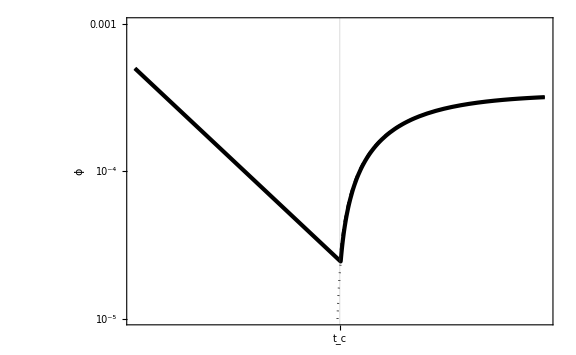

```mathematica
LogPlot[{dotx[t]/.PlotParams,
dotxbar[t]/.PlotParams,
xbarSR'[t]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams},{t,1,3},PlotStyle->{{Black,Dashed},{Black,AbsoluteThickness[3]},{Black,Dotted}},GridLines->{{2},None},PlotRange->{10^-5,10 10^-4},FrameTicks->{None,{{{2,"t_(<c>)"}},None}},FrameLabel->{None,ϕ̇}]
```

```mathematica
ttbarc/.PlotParams
```

1/3 Log[1/(100 (1/100+3 (-1/10000000-xc+xL)))]

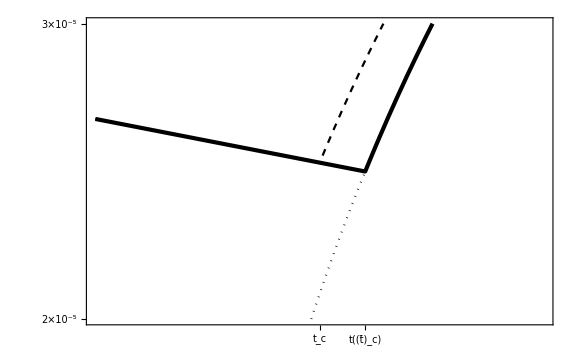

```mathematica
LogPlot[{dotx[t]/.PlotParams,
dotxbar[t]/.PlotParams,
xbarSR'[t]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams},{t,1.98,2.02},PlotStyle->{{Black,Dashed},{Black,AbsoluteThickness[3]},{Black,Dotted}},GridLines->{{2,ttbarc/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams},{dotx[2]/.PlotParams,dotxbar[ttbarc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,xbarSR'[2]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams}},PlotRange->{2 10^-5,3 10^-5},FrameTicks->{{{{dotx[2]/.PlotParams,Subscript[OverDot[ϕ], "c"]},{dotxbar[ttbarc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,Subscript[OverDot[OverBar[ϕ]], "c"]},{xbarSR'[2]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,OverDot[OverBar[ϕ]]["t_(<c>)"]}},None},{{{2,"t_(<c>)"},{ttbarc/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,Style["t",Italic][Subscript[OverBar[Style["t",Italic]], "c"]]}},None}}]
```

```mathematica
ZcIndet[t_]=Integrate[Exp[-3H (t-tc)]/xSR'[t]^2,t]
```

(3 ⅇ^(3 H tc) H)/(F0 (-ⅇ^(3 H t) F0+ⅇ^(3 H tc) F0+3 dotxL ⅇ^(3 H tL) H))

```mathematica
Limit[ZcIndet[t],{t->∞},Assumptions->{H>0}]
```

0

```mathematica
Zc=-ZcIndet[tc]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-1/(dotxc F0)

```mathematica
xSR''[t]// Simplify
```

-ⅇ^(-3 H t) (ⅇ^(3 H tc) F0+3 dotxL ⅇ^(3 H tL) H)

#### quadratic slope

```mathematica
Quit[]
```

```mathematica
xSR[t_]=Simplify[Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-m^2(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]
```

(dotxc (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))))/(Cm-Cp)+xc

```mathematica
xSR'[tc]
```

dotxc

```mathematica
xSR'[t]
```

(dotxc (Cm ⅇ^(Cm (t-tc))-Cp ⅇ^(Cp (t-tc))))/(Cm-Cp)

```mathematica
xSR''[t]
```

(dotxc (Cm^2 ⅇ^(Cm (t-tc))-Cp^2 ⅇ^(Cp (t-tc))))/(Cm-Cp)

```mathematica
Simplify[Normal[Series[(-3H+√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

m^2/(3 H)

```mathematica
Simplify[Normal[Series[(-3H-√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

-3 H-m^2/(3 H)

```mathematica
ZcIndet[t_]=Integrate[Exp[-3H (t-tc)]/xSR'[t]^2/.{Cp->m^2/(3H),Cm->-3H-m^2/(3H)},t]
```

-(3 H (9 H^2+2 m^2))/(dotxc^2 m^2 (9 H^2+(1+ⅇ^(((9 H^2+2 m^2) (t-tc))/(3 H))) m^2))

```mathematica
Limit[ZcIndet[t],{t->∞},Assumptions->{H>0,m>0}]
```

0

```mathematica
Zc=1-3H dotxc^2 ZcIndet[tc]//Simplify
```

1+(9 H^2)/m^2

```mathematica
5/2(h(h-2ηV))/(h-6)^2/.{h->-6}
```

-5/48 (-6-2 ηV)

#### tanh transition (sharp)

```mathematica
Quit[]
```

```mathematica
Vp[x_]=F0/2(1+Tanh[x/dx]);
```

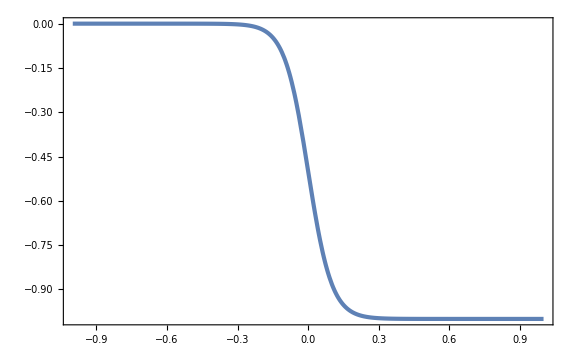

```mathematica
Plot[Vp[x]/.{F0->-1,dx->0.1},{x,-1,1}]
```

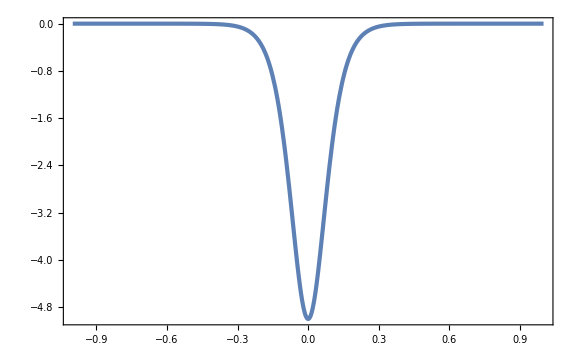

```mathematica
Plot[Vp'[x]/.{F0->-1,dx->0.1},{x,-1,1},PlotRange->Full]
```

```mathematica
Hs=10^-4;
ϵSRs=10^-2;
ASRs=10^-9;
AUSRcs=10^-2;
```

```mathematica
F0s=F0/.Solve[1/2 F0^2/(3 Hs^2)==ASRs&&F0<0,F0][[1]];F0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[10^-2/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

-7.74597×10^-9

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNs=10^-2;
dxs=dotxcs dNs/Hs;dxs//N
```

1.59155×10^-6

```mathematica
params={H->Hs,F0->F0s,dotxL->dotxLs,xL->xLs,dx->dxs};
```

```mathematica
tf=(NLs+3)/Hs;tf//N
```

52632.1

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ϵsol[t_]=dotxsol[t]^2/(2 Hs^2);
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hs dotxsol[t])/.params;
```

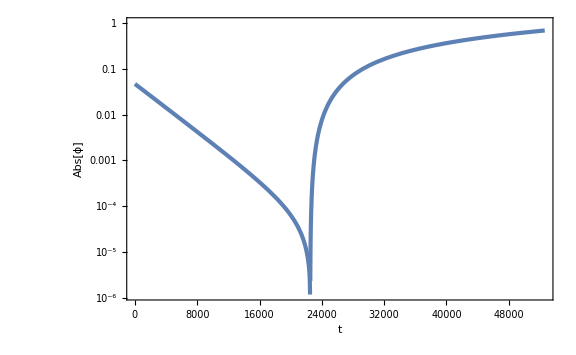

```mathematica
LogPlot[Abs[xsol[t]],{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

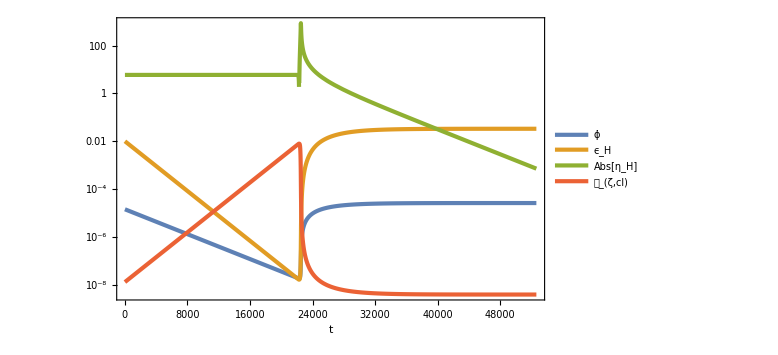

```mathematica
LogPlot[{dotxsol[t],ϵsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hs/(2π))^2},{t,0,tf},PlotRange->Full,PlotLegends->{OverDot[ϕ],Subscript[ϵ, H],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl]},FrameLabel->{t,None}]
```

```mathematica
deltax=Hs/(2π);
```

```mathematica
barsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xbar[t_]=x[t]/.barsol;
dotxbar[t_]=x'[t]/.barsol;
```

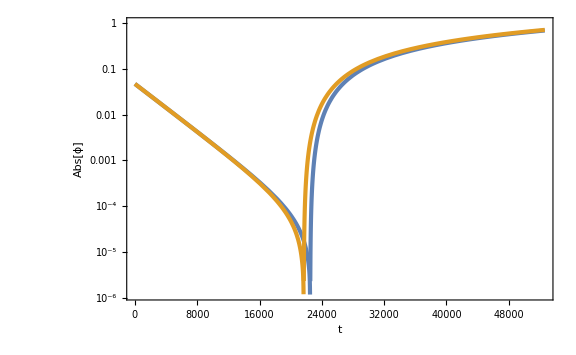

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xbar[t]]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

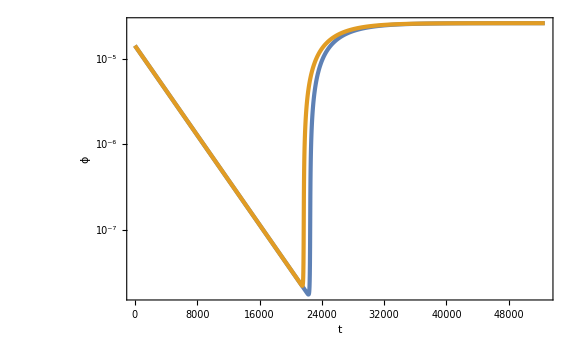

```mathematica
LogPlot[{dotxsol[t],dotxbar[t]},{t,0,tf},FrameLabel->{t,OverDot[ϕ]}]
```

```mathematica
xf=xsol[tf-1/Hs]
```

0.4340526374348987687838267584

```mathematica
ζL=Hs((t/.FindRoot[xbar[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

-0.08301099280070268085393075666

```mathematica
tS=1/Hs;
```

```mathematica
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]];
```

NDSolve::precw: The precision of the differential equation ({{-(√(3/5) (1+Tanh[Times[«3»]]))/200000000+(3 x'[t])/10000+x''[t]==0,x[10000]==-0.0022780177685517181779696572245,x'[10000]==7.04095473290232144184214765×10^-7},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
```

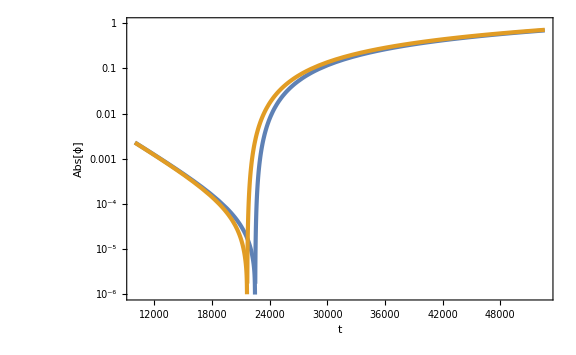

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xSsol[t]]},{t,tS,tf},FrameLabel->{t,Abs[ϕ]}]
```

```mathematica
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1»==0.4340526374348987687838267584) is less than WorkingPrecision (30.).

-0.08301099469433590651472030798

```mathematica
ζS/ζL
```

1.00000002281183686366849609

```mathematica
dotxczetaLPS=ParallelTable[bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Hs((t/.FindRoot[xsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))//Quiet;
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))-ζL//Quiet;
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];//AbsoluteTiming
```

{8.48268,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(2.2751469824419948570978×10^-18)/x^2

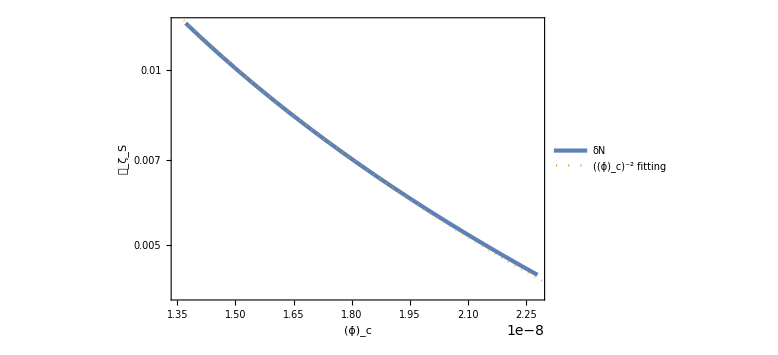

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{Subscript[OverDot[ϕ], "c"],Subscript[𝒫, Subscript[ζ, "S"]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-8,10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[OverDot[ϕ], "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.00689082524014306402145836787

```mathematica
fNL=PSvszetaLint'[0]/PS0
```

5.195401726503492072148772

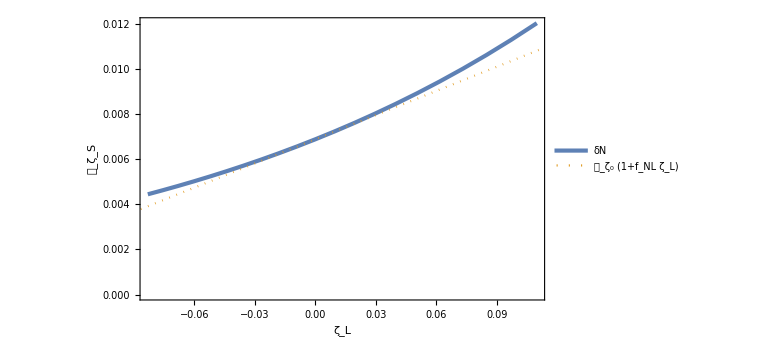

```mathematica
Show[ListPlot[PSvszetaL,FrameLabel->{Subscript[ζ, "L"],Subscript[𝒫, Subscript[ζ, "S"]]},PlotLegends->{Style[δN,Italic]}],Plot[PS0(1+fNL x),{x,-1,1},PlotStyle->{Color[2],Dotted},PlotLegends->{Subscript[𝒫, Subscript[ζ, "S"0]](1+Subscript[f, NL] Subscript[ζ, "L"])}]]
```

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t],x''[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ddotxsol[t_]=x''[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet
dotxc=dotxsol[tc]
```

22342.6825988886125295590267602

1.81952054653249756629981×10^-8

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

-1.94949537400849883383

```mathematica
Zc=NIntegrate[Exp[-3Hs (t-tc)]/dotxsol[t]^2,{t,tc,tf}]
```

2.86593×10^17

```mathematica
1/(3Hs dotxc^2)
```

1.00685009883165822059508×10^19

```mathematica
Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])
```

4.775968781440159215005204024×10^12

```mathematica
Ztildec=1/(3Hs dotxc^2)+Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])+Zc
```

1.03551×10^19

```mathematica
-power/(Hs dotxc^2 Ztildec)
```

5.68662

#### tanh transition (smooth)

```mathematica
Quit[]
```

```mathematica
Vp[x_]=F0/2(1+Tanh[x/dx]);
```

```mathematica
Plot[Vp[x]/.{F0->-1,dx->0.1},{x,-1,1}]
```

-Graphics-

```mathematica
Plot[Vp'[x]/.{F0->-1,dx->0.1},{x,-1,1},PlotRange->Full]
```

-Graphics-

```mathematica
Hs=10^-4;
ϵSRs=10^-2;
ASRs=10^-9;
AUSRcs=10^-2;
```

```mathematica
F0s=F0/.Solve[1/2 F0^2/(3 Hs^2)==ASRs&&F0<0,F0][[1]];F0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[10^-2/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

-7.74597×10^-9

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNs=10;
dxs=dotxcs dNs/Hs;dxs//N
```

0.00159155

```mathematica
params={H->Hs,F0->F0s,dotxL->dotxLs,xL->-3dxs+xLs,dx->dxs};
```

```mathematica
Cp=(-Vp'[0])/(3Hs)/.params;Cp//N
Cm=-3Hs;Cm//N
```

0.00811156

-0.0003

```mathematica
tf=(NLs+2+3)/Hs;tf//N
```

72632.1

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ϵsol[t_]=dotxsol[t]^2/(2 Hs^2);
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hs dotxsol[t])/.params;
```

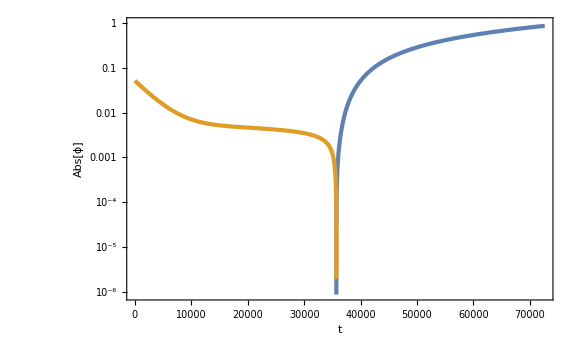

```mathematica
LogPlot[{xsol[t],-xsol[t]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

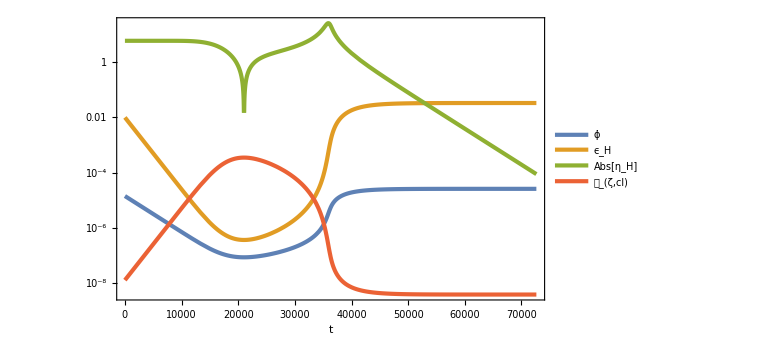

```mathematica
LogPlot[{dotxsol[t],ϵsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hs/(2π))^2},{t,0,tf},PlotRange->Full,PlotLegends->{ϕ̇,Subscript[ϵ, H],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl]},FrameLabel->{t,None}]
```

```mathematica
deltax=Hs/(2π);
```

```mathematica
barsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xbar[t_]=x[t]/.barsol;
dotxbar[t_]=x'[t]/.barsol;
```

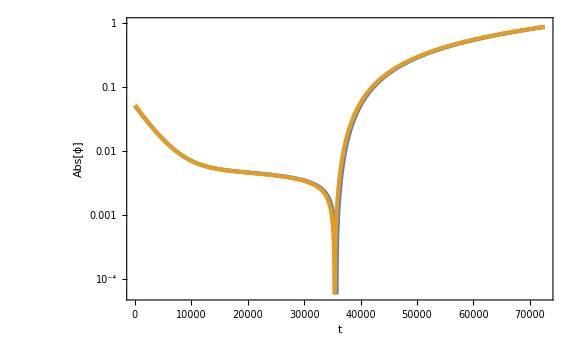

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xbar[t]]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

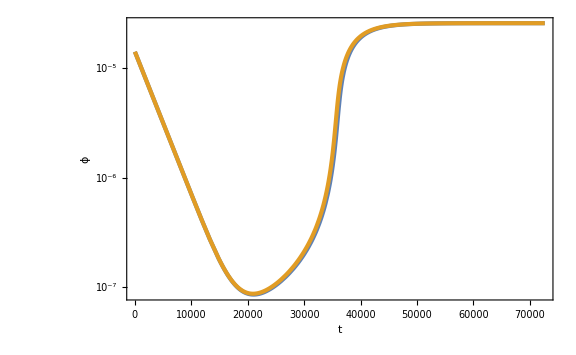

```mathematica
LogPlot[{dotxsol[t],dotxbar[t]},{t,0,tf},FrameLabel->{t,ϕ̇}]
```

```mathematica
xf=xsol[tf-1/Hs]
```

0.61365699454201893113477054563

```mathematica
ζL=Hs((t/.FindRoot[xbar[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1»[t]==0.61365699454201893113477054563) is less than WorkingPrecision (30.).

-0.0295023456476593789750730534

```mathematica
tS=1/Hs;
```

```mathematica
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]];
```

NDSolve::precw: The precision of the differential equation ({{-(√(3/5) (1+Tanh[Times[«3»]]))/200000000+(3 x'[t])/10000+x''[t]==0,x[10000]==-0.0070520745247806800805842837272,x'[10000]==7.04870496738533348527088153×10^-7},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
```

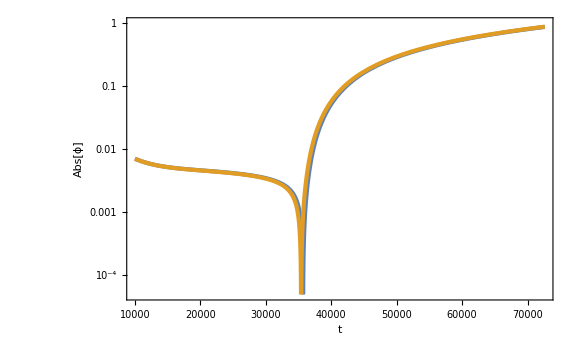

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xSsol[t]]},{t,tS,tf},FrameLabel->{t,Abs[ϕ]}]
```

```mathematica
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

-0.0293917504380982125425312155

```mathematica
ζS/ζL
```

0.996251307916937082592704551

```mathematica
dotxczetaLPS=ParallelTable[bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Hs((t/.FindRoot[xsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))//Quiet;
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))-ζL//Quiet;
{dotxc,ζL,ζS^2},{i,-10,10}];//AbsoluteTiming
```

{6.32519,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(7.392758202447947422783373×10^-18)/x^2

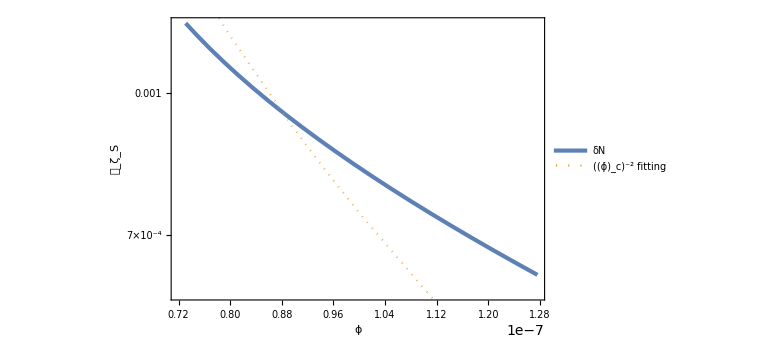

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-8,10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.00086387499381544646892392754

```mathematica
fNL=PSvszetaLint'[0]/PS0
```

1.06854037702752625266004

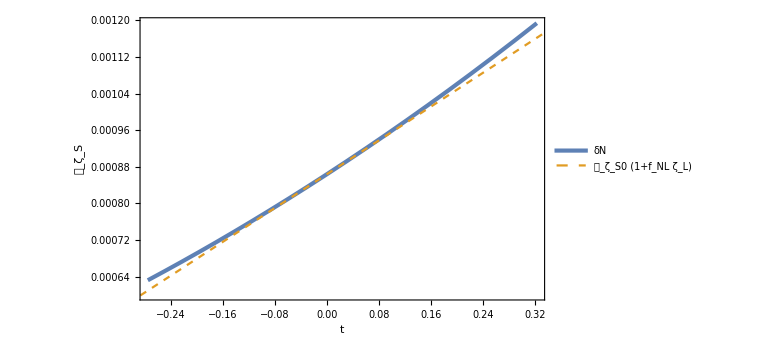

```mathematica
Show[ListPlot[PSvszetaL,FrameLabel->{t,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],Plot[{PS0(1+fNL x)},{x,-1,1},PlotStyle->{{Color[2],Dashed}},PlotLegends->{Subscript[𝒫, Subscript[ζ, S0]](1+Subscript[f, NL] Subscript[ζ, "L"])}]]
```

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t],x''[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ddotxsol[t_]=x''[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet
dotxc=dotxsol[tc]
```

18436.8834694940933692150766359

9.6282866880557489440508056×10^-8

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

-1.1009519594228090841881

```mathematica
Zc=NIntegrate[Exp[-3Hs(t-tc)]/dotxsol[t]^2,{t,tc,tf}]
```

3.84867×10^17

```mathematica
1/(3Hs dotxc^2)
```

3.595677387708396186126241×10^17

```mathematica
Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])
```

2.95465257739263189451541264×10^10

```mathematica
Ztildec=1/(3Hs dotxc^2)+Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])+Zc
```

7.44434×10^17

```mathematica
-power/(Hs dotxc^2 Ztildec)
```

1.59531

#### tanh transition (smooth, early c)

```mathematica
Quit[]
```

```mathematica
Vp[x_]=F0/2(1+Tanh[x/dx]);
```

```mathematica
Plot[Vp[x]/.{F0->-1,dx->0.1},{x,-1,1}]
```

-Graphics-

```mathematica
Plot[Vp'[x]/.{F0->-1,dx->0.1},{x,-1,1},PlotRange->Full]
```

-Graphics-

```mathematica
Hs=10^-4;
ϵSRs=10^-2;
ASRs=10^-9;
AUSRcs=10^-2;
```

```mathematica
F0s=F0/.Solve[1/2 F0^2/(3 Hs^2)==ASRs&&F0<0,F0][[1]];F0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[10^-2/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

-7.74597×10^-9

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNs=10;
dxs=dotxcs dNs/Hs;dxs//N
```

0.00159155

```mathematica
params={H->Hs,F0->F0s,dotxL->dotxLs,xL->-3dxs+xLs,dx->dxs};
```

```mathematica
Cp=(-Vp'[0])/(3Hs)/.params;Cp//N
Cm=-3Hs;Cm//N
```

0.00811156

-0.0003

```mathematica
tf=(NLs+2+3)/Hs;tf//N
```

72632.1

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ϵsol[t_]=dotxsol[t]^2/(2 Hs^2);
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hs dotxsol[t])/.params;
```

```mathematica
LogPlot[{xsol[t],-xsol[t]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

-Graphics-

```mathematica
1/Hs
```

10000

```mathematica
LogPlot[{dotxsol[t],ϵsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hs/(2π))^2},{t,0,tf},PlotRange->Full,PlotLegends->{ϕ̇,Subscript[ϵ, H],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl]},FrameLabel->{t,None}]
```

-Graphics-

```mathematica
deltax=Hs/(2π);
```

```mathematica
barsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xbar[t_]=x[t]/.barsol;
dotxbar[t_]=x'[t]/.barsol;
```

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xbar[t]]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

-Graphics-

```mathematica
LogPlot[{dotxsol[t],dotxbar[t]},{t,0,tf},FrameLabel->{t,ϕ̇}]
```

-Graphics-

```mathematica
xf=xsol[tf-1/Hs]
```

0.61365699454201893113477054563

```mathematica
ζL=Hs((t/.FindRoot[xbar[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1»[t]==0.61365699454201893113477054563) is less than WorkingPrecision (30.).

-0.0295023456476593789750730534

```mathematica
tS=1/Hs;
```

```mathematica
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]];
```

NDSolve::precw: The precision of the differential equation ({{-(√(3/5) (1+Tanh[Times[«3»]]))/200000000+(3 x'[t])/10000+x''[t]==0,x[10000]==-0.0070520745247806800805842837272,x'[10000]==7.04870496738533348527088153×10^-7},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
```

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xSsol[t]]},{t,tS,tf},FrameLabel->{t,Abs[ϕ]}]
```

-Graphics-

```mathematica
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

-0.0293917504380982125425312155

```mathematica
ζS/ζL
```

0.996251307916937082592704551

```mathematica
xc=xsol[1/Hs]
```

-0.0070679900190898696141611721035

```mathematica
xL/.params//N
```

-0.051862

```mathematica
Hs/(2π)//N
```

0.0000159155

```mathematica
dotxczetaLPS=ParallelTable[bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Hs((t/.FindRoot[xsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))//Quiet;
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))-ζL//Quiet;
{dotxc,ζL,ζS^2},{i,-10,10}];//AbsoluteTiming
```

{6.09886,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(4.3980891927516845513174104×10^-16)/x^2

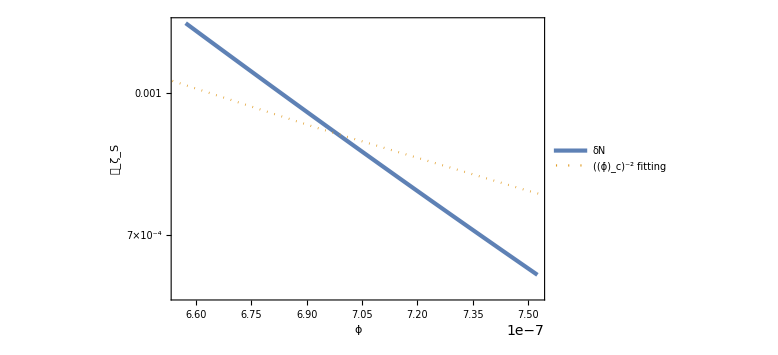

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-7,3 10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.00086387499381544646892392754

```mathematica
fNL=PSvszetaLint'[0]/PS0
```

1.06854037702752625266004

```mathematica
Show[ListPlot[PSvszetaL,FrameLabel->{t,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],Plot[{PS0(1+fNL x)},{x,-1,1},PlotStyle->{{Color[2],Dashed}},PlotLegends->{Subscript[𝒫, Subscript[ζ, S0]](1+Subscript[f, NL] Subscript[ζ, "L"])}]]
```

-Graphics-

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t],x''[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ddotxsol[t_]=x''[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet
dotxc=dotxsol[tc]
```

10000.

7.0487049673853334852708815×10^-7

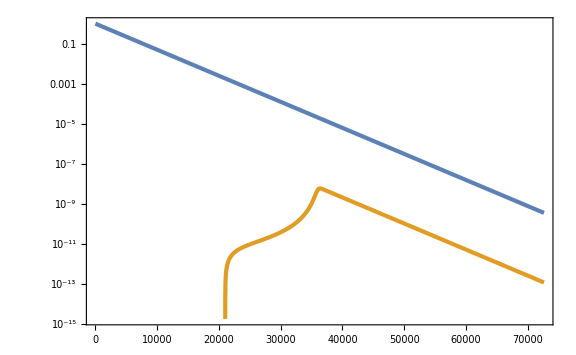

```mathematica
LogPlot[{Exp[-3Hs t],ddotxsol[t]},{t,0,tf}]
```

```mathematica
1/Hs//N
```

10000.

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

-4.6959508620483684526679

```mathematica
Zc=NIntegrate[Exp[-3Hs (t-tc)]/dotxsol[t]^2,{t,tc,tf}]
```

8.17322×10^16

```mathematica
1/(3Hs dotxc^2)
```

6.7090353362010074952496541×10^15

```mathematica
Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])
```

2.351141899901860325985013393×10^9

```mathematica
Ztildec=1/(3Hs dotxc^2)+Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])+Zc
```

8.84412×10^16

```mathematica
-power/(Hs dotxc^2 Ztildec)
```

1.06869

```mathematica
fNL
```

1.06854037702752625266004

### linear slope reparam.

```mathematica
Quit[]
```

```mathematica
$Assumptions={H>0};
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-(√(2ϵ0))/Mpl V0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc],V0->3 Mpl^2 H^2}//Simplify
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)+xc+1/3 √2 Mpl (-1+ⅇ^(3 H (-t+tc))+3 H t-3 H tc) √ϵ0

```mathematica
η1[t_]=xSR''[t]/(H xSR'[t])//Simplify
η2[t_]=η1'[t]/(H η1[t])//Simplify
```

(-3 dotxL ⅇ^(3 H tL)+3 √2 ⅇ^(3 H tc) H Mpl √ϵ0)/(dotxL ⅇ^(3 H tL)+√2 (ⅇ^(3 H t)-ⅇ^(3 H tc)) H Mpl √ϵ0)

-(3 √2 ⅇ^(3 H t) H Mpl √ϵ0)/(dotxL ⅇ^(3 H tL)+√2 (ⅇ^(3 H t)-ⅇ^(3 H tc)) H Mpl √ϵ0)

```mathematica
(3+η1[t]+η2[t])/η1[t]//Simplify
```

0

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H (dxL-xc+xL))/(3 H)+1/3 √2 Mpl √ϵ0 (-1+3 H (t-tL)+(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))-Log[dotxL/(dotxL+3 H (dxL-xc+xL))])

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+δ xi0]==xSR[t]/.{dxL->δ dxL}]/.{tc->tcUSR}]
```

1/3 ((dotxL ⅇ^(3 H (-t+tL)))/H-(dotxL ⅇ^(-3 H (t-tL+xi0 δ)))/H+3 dxL δ-(√2 dotxL ⅇ^(3 H (-t+tL)) Mpl √ϵ0)/(dotxL-3 H xc+3 H xL)+3 √2 H Mpl xi0 δ √ϵ0+(√2 dotxL ⅇ^(-3 H (t-tL+xi0 δ)) Mpl √ϵ0)/(dotxL+3 H (-xc+xL+dxL δ))+√2 Mpl √ϵ0 Log[dotxL/(dotxL-3 H xc+3 H xL)]-√2 Mpl √ϵ0 Log[dotxL/(dotxL+3 H (-xc+xL+dxL δ))])==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{δ,0,1}]]/.{δ->1}//Simplify
```

dxL+dotxL ⅇ^(3 H (-t+tL)) xi0+√2 H Mpl xi0 √ϵ0+(√2 dxL H Mpl √ϵ0)/(dotxL+3 H (-xc+xL))==(√2 dotxL ⅇ^(3 H (-t+tL)) H Mpl (dxL+xi0 (dotxL+3 H (-xc+xL))) √ϵ0)/(dotxL+3 H (-xc+xL))^2

```mathematica
xi0SR[t_]=xi0/.Simplify[Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(-dotxc dxL+√2 dxL (-1+ⅇ^(3 H (-t+tc))) H Mpl √ϵ0)/(dotxc (dotxc ⅇ^(3 H (-t+tc))-√2 (-1+ⅇ^(3 H (-t+tc))) H Mpl √ϵ0))

```mathematica
-δ/Limit[xi0SR[t]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]^2 D[Limit[xi0SR[t]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]^2, δ]//Simplify
```

2/(1+δ)

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

```mathematica
ϵHUSR[t_]=xUSR'[t]^2/(2 H^2)//Simplify
```

(dotxL^2 ⅇ^(6 H (-t+tL)))/(2 H^2)

```mathematica
xi0dotUSR[t_]=Normal[Series[xi0USR'[t]/.{dxL->-zetaL dotxL/H}//Simplify,{zetaL,0,1}]]
```

3 ⅇ^(3 H t-3 H tL) zetaL

```mathematica
xi0dotUSR[t]/(1/(H Exp[3H t]ϵHUSR[t]))//Simplify
```

(3 dotxL^2 ⅇ^(3 H tL) zetaL)/(2 H)

```mathematica
ϵHSR[t_]=xSR'[t]^2/(2 H^2)/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

((dotxc ⅇ^(3 H (-t+tc))-√2 (-1+ⅇ^(3 H (-t+tc))) H Mpl √ϵ0)^2)/(2 H^2)

```mathematica
xi0dotSR[t_]=Normal[Series[xi0SR'[t]/.{dxL->-zetaLc dotxc/H}//Simplify,{zetaLc,0,1}]]
```

(3 dotxc^2 ⅇ^(3 H (-t+tc)) zetaLc)/((dotxc ⅇ^(3 H (-t+tc))-√2 (-1+ⅇ^(3 H (-t+tc))) H Mpl √ϵ0)^2)

```mathematica
xi0dotSR[t]/(1/(H Exp[3H t]ϵHSR[t]))//Simplify
```

(3 dotxc^2 ⅇ^(3 H tc) zetaLc)/(2 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-(3 √2 dxL ⅇ^(3 H (-t+tc)) H^2 Mpl √ϵ0)/dotxc

```mathematica
Normal[Series[Simplify[xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,-1}]]/.{δ->dotxc/(√(2ϵ0)Mpl H)}//Simplify
```

-(3 √2 dxL ⅇ^(3 H (-t+tc)) H^2 Mpl √ϵ0)/dotxc

```mathematica
Simplify[xSR'[t]xi0SR'[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

-(3 dxL ⅇ^(3 H (-t+tc)) H δ)/(1+ⅇ^(3 H (-t+tc)) (-1+δ))

```mathematica
Limit[Simplify[(xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t])/(xSR''[t]xi0SR[t])/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]
```

1/(1-δ^2)

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

(3 √2 dotxL ⅇ^(3 H (-t+tL)) H^2 Mpl √ϵ0)/dotxc^2

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

(dotxc^2 ⅇ^(3 H (t-tL)))/(√2 dotxL H Mpl √ϵ0)

bispectrum correction reads

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->-dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-6 Ps zetaL

```mathematica
Limit[3H dotxc^2 Exp[-3H(t-tc)]/(xSR'[t]xSR''[t])/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]
```

-δ^2/(-1+δ)

```mathematica
3H dotxc^2 Integrate[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify,{t,tc,∞}]
```

$Aborted

```mathematica
Normal[Series[Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{t->tc+dt}],{dt,0,1}]]
```

1/dotxc^2+(3 dt (dotxc H-2 √2 H^2 Mpl √ϵ0))/dotxc^3

```mathematica
Solve[1==3dt(dotxc H-2 √(2ϵ0)Mpl H^2)/dotxc,dt]
```

{{dt→-dotxc/(3 H (-dotxc+2 √2 H Mpl √ϵ0))}}

```mathematica
dtanal=Normal[Series[dt/.Solve[1==3dt(dotxc H-2 √(2ϵ0)Mpl H^2)/dotxc,dt][[1]]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,1}]]/.{δ->dotxc/(√(2ϵ0)Mpl H)}
```

-dotxc/(6 √2 H^2 Mpl √ϵ0)

```mathematica
Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]
```

ⅇ^(3 H (t-tc))/((dotxc+√2 (-1+ⅇ^(3 H (t-tc))) H Mpl √ϵ0)^2)

```mathematica
Normal[Series[Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,1}]]
```

ⅇ^(3 H (t-tc))/(2 (-1+ⅇ^(3 H (t-tc)))^2 H^2 Mpl^2 ϵ0)-(ⅇ^(3 H (t-tc)) δ)/((-1+ⅇ^(3 H (t-tc)))^3 H^2 Mpl^2 ϵ0)

```mathematica
Normal[Series[Normal[Series[Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,1}]]/.{t->tc+dt}//Simplify,{dt,0,1}]]
```

(-1-δ)/(24 H^2 Mpl^2 ϵ0)-δ/(27 dt^3 H^5 Mpl^2 ϵ0)+(dt δ)/(80 H Mpl^2 ϵ0)+(1+δ)/(18 dt^2 H^4 Mpl^2 ϵ0)

```mathematica
Zcanal[δ_]=3H dotxc^2 dtanal/dotxc^2/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

-δ/2

```mathematica
Zcintegrand[δ_]=Simplify[3H dotxc^2 Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

(3 ⅇ^(3 H (t-tc)) H δ^2)/((-1+ⅇ^(3 H (t-tc))+δ)^2)

```mathematica
Integrate[Zcintegrand[δ],t]/.{t->tc}
```

-δ

```mathematica
Zc[δ_]=Limit[Integrate[Zcintegrand[δ],t],{t->∞},Assumptions->{H>0}]-Integrate[Zcintegrand[δ],t]/.{t->tc}
```

δ

### linear-quadratic slope

```mathematica
Quit[]
```

```mathematica
$Assumptions={H>0,Mpl>0,ϵ0>0,η0<0,3-4η0>0,s>3,dxL>0,δ>0,tc>tL,dotxL>0,dotxc>0};
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xSR[t_]=Simplify[Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-(√(2ϵ0))/Mpl V0+η0/Mpl^2 V0(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc],V0->3 Mpl^2 H^2}]/.{3-4η0->s^2/3,9-12η0->s^2}//Simplify
```

(dotxL ⅇ^(1/2 H (-(3+s) t+(-3+s) tc+6 tL)) (-1+ⅇ^(H s (t-tc))))/(H s)+xc-(ⅇ^(-1/2 H ((3+s) t-(-3+s) tc)) Mpl (ⅇ^(3 H tc) (-3+s)-2 ⅇ^(1/2 H ((3+s) t-(-3+s) tc)) s+ⅇ^(H (s (t-tc)+3 tc)) (3+s)) √ϵ0)/(√2 s η0)

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc+(dotxL ⅇ^(1/6 (-3 H (3+s) (t-tL)+(-3+s) Log[dotxL/(dotxL+3 H (dxL-xc+xL))])) (-1+ⅇ^(H s (t-tL)) (dotxL/(dotxL+3 H (dxL-xc+xL)))^(-s/3)))/(H s)-1/(√2 s η0)ⅇ^(1/6 (-3 H (3+s) t+3 H (-3+s) tL+(-3+s) Log[dotxL/(dotxL+3 H (dxL-xc+xL))])) Mpl (-2 ⅇ^(1/2 H ((3+s) t-(-3+s) (tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)))) s+ⅇ^(H (s (t-tL)+3 tL)) (3+s) (dotxL/(dotxL+3 H (dxL-xc+xL)))^(1-s/3)+(dotxL ⅇ^(3 H tL) (-3+s))/(dotxL+3 H (dxL-xc+xL))) √ϵ0

```mathematica
xbarSR''[t]+3H xbarSR'[t]-(√(2ϵ0))/Mpl V0+η0/Mpl^2 V0(xbarSR[t]-xc)/.{s->Sqrt[9-12η0],V0->3 Mpl^2 H^2}//Simplify
```

0

```mathematica
xbarSR[ttbarc]//Simplify
```

xc

```mathematica
xbarSR'[ttbarc]//Simplify
```

dotxL+3 H (dxL-xc+xL)

```mathematica
xi0Eq={xbarSR[t+σ xi0]==xSR[t]/.{dxL->σ dxL}/.{tc->tcUSR}};
```

```mathematica
xi0Eqlinear=Simplify[Normal[Series[xi0Eq,{σ,0,1}]]]/.{σ->1}//Simplify
```

{xi0 (-ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (3+s) (dotxL/(dotxL+3 H (-xc+xL)))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))+1/(dotxL+3 H (-xc+xL))dxL (-ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (-3+s) (dotxL/(dotxL+3 H (-xc+xL)))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))==0}

```mathematica
xi0SR[t_]=Collect[xi0/.Simplify[Simplify[Solve[xi0Eqlinear[[1]],xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxL->dotxc Exp[3H(tc-tL)]},dxL,Simplify]
```

-(dxL (-ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxc η0)+ⅇ^(H (3+s) t+H s (tc-tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0+2 dotxc η0)))/(dotxc (-ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxc η0)+ⅇ^(H (3+s) t+H s (tc-tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0+2 dotxc η0)))

```mathematica
Simplify[Normal[Series[xi0SR[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]]/.{Sqrt[ϵ0]->π0/(Sqrt[2]Mpl H)}//Simplify
```

-(dxL (dotxc ⅇ^(3 H t)+(ⅇ^(3 H t)-ⅇ^(3 H tc)) π0))/(dotxc (dotxc ⅇ^(3 H tc)+(ⅇ^(3 H t)-ⅇ^(3 H tc)) π0))

```mathematica
xi0SR[t]/.{ϵ0->0}//Simplify
```

-(dxL (ⅇ^(H s tc) (-3+s)+ⅇ^(H s t) (3+s)))/(dotxc (ⅇ^(H s t) (-3+s)+ⅇ^(H s tc) (3+s)))

```mathematica
xi0δ[t_,δ_]=xi0SR[t]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

(dxL (ⅇ^(H s t) (3+s) (-3+s-2 δ η0)-ⅇ^(H s tc) (-3+s) (3+s+2 δ η0)))/(√2 H Mpl δ √ϵ0 (-ⅇ^(H s t) (-3+s) (3+s-2 δ η0)+ⅇ^(H s tc) (3+s) (-3+s+2 δ η0)))

```mathematica
Limxi0=Limit[xi0SR[t],{t->∞}]
```

(dxL (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxc η0))/(dotxc (-3+s) (-√2 H Mpl (3+s) √ϵ0+2 dotxc η0))

```mathematica
Simplify[-dotxc/Limxi0^2 D[(Limxi0^2), dotxc]]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

(2 (-9+s^2+12 δ η0-4 s δ η0+4 δ^2 η0^2))/(-9+s^2-4 s δ η0+4 δ^2 η0^2)

```mathematica
powern[t_]=-δ/xi0δ[t,δ]^2 D[(xi0δ[t,δ]^2), δ]//Simplify
```

(2 (ⅇ^(2 H s t) (-9+s^2) (-9+s^2+12 δ η0-4 s δ η0+4 δ^2 η0^2)+ⅇ^(2 H s tc) (-9+s^2) (-9+s^2+12 δ η0+4 s δ η0+4 δ^2 η0^2)-2 ⅇ^(H s (t+tc)) (s^4-2 s^2 (9-6 δ η0+2 δ^2 η0^2)-9 (-9+12 δ η0+4 δ^2 η0^2))))/((ⅇ^(H s t) (-3+s) (3+s-2 δ η0)-ⅇ^(H s tc) (3+s) (-3+s+2 δ η0)) (ⅇ^(H s t) (3+s) (-3+s-2 δ η0)-ⅇ^(H s tc) (-3+s) (3+s+2 δ η0)))

```mathematica
Limit[powern[t],{t->∞}]
```

(2 (-9+s^2+12 δ η0-4 s δ η0+4 δ^2 η0^2))/((-3+s-2 δ η0) (3+s-2 δ η0))

```mathematica
Limit[Normal[Series[powern[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify,{t->∞}]
```

2/(1+δ)

```mathematica
Limit[powern[t],{δ->∞}]//Simplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

2

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

```mathematica
Coeff[t]=Collect[xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,dxL,Simplify]
```

(dxL H (96 ⅇ^(1/2 H ((9+5 s) t+(3+s) tc-4 s tL)) s^2 δ^2 η0^2 (ⅇ^(H s t) (-3+s) (3+s-2 δ η0)-ⅇ^(H s tc) (3+s) (-3+s+2 δ η0))+ⅇ^(1/2 H (3 (3+s) t-(-3+s) tc-4 s tL)) (-ⅇ^(H s t) (-3+s) (3+s-2 δ η0)+ⅇ^(H s tc) (3+s) (-3+s+2 δ η0)) (ⅇ^(H s t) (-3+s)^2 (3+s-2 δ η0)+ⅇ^(H s tc) (3+s)^2 (-3+s+2 δ η0)) (-ⅇ^(H s t) (3+s) (-3+s-2 δ η0)+ⅇ^(H s tc) (-3+s) (3+s+2 δ η0))))/(8 s δ η0 (ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (3+s-2 δ η0)-ⅇ^(H (3+s) t+H s (tc-tL)) (3+s) (-3+s+2 δ η0))^2)

```mathematica
Correction[t_]=Coeff[t]/(xSR''[t]xi0SR[t])/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

(ⅇ^(1/2 H (-(3+s) t+(-3+s) tc+2 s tL)) (-ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (3+s-2 δ η0)+ⅇ^(H (3+s) t+H s (tc-tL)) (3+s) (-3+s+2 δ η0)) (96 ⅇ^(1/2 H ((9+5 s) t+(3+s) tc-4 s tL)) s^2 δ^2 η0^2 (ⅇ^(H s t) (-3+s) (3+s-2 δ η0)-ⅇ^(H s tc) (3+s) (-3+s+2 δ η0))+ⅇ^(1/2 H (3 (3+s) t-(-3+s) tc-4 s tL)) (-ⅇ^(H s t) (-3+s) (3+s-2 δ η0)+ⅇ^(H s tc) (3+s) (-3+s+2 δ η0)) (ⅇ^(H s t) (-3+s)^2 (3+s-2 δ η0)+ⅇ^(H s tc) (3+s)^2 (-3+s+2 δ η0)) (-ⅇ^(H s t) (3+s) (-3+s-2 δ η0)+ⅇ^(H s tc) (-3+s) (3+s+2 δ η0))))/((ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (3+s-2 δ η0)-ⅇ^(H (3+s) t+H s (tc-tL)) (3+s) (-3+s+2 δ η0))^2 (ⅇ^(H s t) (-3+s)^2 (3+s-2 δ η0)+ⅇ^(H s tc) (3+s)^2 (-3+s+2 δ η0)) (-ⅇ^(H s t) (3+s) (-3+s-2 δ η0)+ⅇ^(H s tc) (-3+s) (3+s+2 δ η0)))

```mathematica
Zcintegrand[t_]=Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

(8 ⅇ^(H s (t+tc)) s^2 η0^2)/(H^2 Mpl^2 ϵ0 (ⅇ^(H s t) (-3+s) (3+s-2 δ η0)-ⅇ^(H s tc) (3+s) (-3+s+2 δ η0))^2)

```mathematica
Zcint[t_]=Integrate[Zcintegrand[t],t]//Simplify
```

(8 ⅇ^(H s tc) s η0^2)/(H^3 Mpl^2 (-3+s) ϵ0 (3+s-2 δ η0) (-ⅇ^(H s t) (-3+s) (3+s-2 δ η0)+ⅇ^(H s tc) (3+s) (-3+s+2 δ η0)))

```mathematica
Zc[t_]=1+3H dotxc^2(Zcint[t]-Zcint[tc]+Exp[-3H (t-tc)]/(xSR''[t]xSR'[t]))/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

1-(12 δ η0)/((-3+s) (3+s-2 δ η0))+(48 s δ^2 η0^2 (ⅇ^(H s tc)/((-3+s) (3+s-2 δ η0))-(2 ⅇ^(H s (t+tc)) s)/(ⅇ^(H s t) (-3+s)^2 (3+s-2 δ η0)+ⅇ^(H s tc) (3+s)^2 (-3+s+2 δ η0))))/(-ⅇ^(H s t) (-3+s) (3+s-2 δ η0)+ⅇ^(H s tc) (3+s) (-3+s+2 δ η0))

```mathematica
fNL[t_]=Correction[t](5powern[t])/(4Zc[t])//Simplify
```

(5 (ⅇ^(2 H s t) (-9+s^2) (-9+s^2+12 δ η0-4 s δ η0+4 δ^2 η0^2)+ⅇ^(2 H s tc) (-9+s^2) (-9+s^2+12 δ η0+4 s δ η0+4 δ^2 η0^2)-2 ⅇ^(H s (t+tc)) (s^4-2 s^2 (9-6 δ η0+2 δ^2 η0^2)-9 (-9+12 δ η0+4 δ^2 η0^2))))/(2 (ⅇ^(H s t) (3+s) (-3+s-2 δ η0)-ⅇ^(H s tc) (-3+s) (3+s+2 δ η0))^2)

```mathematica
fNLLim=Limit[fNL[t],{t->∞}]//FullSimplify
```

(5 (-3+s) (-9+12 δ η0+(s-2 δ η0)^2))/(2 (3+s) (-3+s-2 δ η0)^2)

```mathematica
(5(3-s)(9-12δ η0-(s-2δ η0)^2))/(2(3+s)(3-s+2δ η0)^2)-fNLLim//Simplify
```

0

```mathematica
fNLSuyama=-(5(-2Sqrt[3]+δ(Sqrt[3]-Sqrt[3-4η0]))(3+δ(-3+Sqrt[9-12η0])-δ^2 η0))/(2(2Sqrt[3]+δ(Sqrt[3]+Sqrt[3-4η0]))(3+δ Sqrt[9-12η0]-δ^2 η0))//Simplify
```

-(5 (-2 √3+δ (√3-√(3-4 η0))) (3+δ (-3+√(9-12 η0))-δ^2 η0))/(2 (2 √3+δ (√3+√(3-4 η0))) (3+δ √(9-12 η0)-δ^2 η0))

```mathematica
fNLLim-fNLSuyama/.{s->Sqrt[9-12η0]}//Simplify
```

0

```mathematica
Normal[Series[fNLLim/.{s->Sqrt[9-12η0]}//Simplify,{η0,0,0}]]//Simplify
```

5/(2 (1+δ)^2)

```mathematica
Normal[Series[Simplify[fNLLim/.{δ->1/h}]/.{h->0,s->Sqrt[9-12η0]}//Simplify,{η0,0,1}]]/.{η0->-m^2/(3 H^2)}
```

(5 m^2)/(18 H^2)

```mathematica
LimCor=Limit[Correction[t],{t->∞}]
Limn=Limit[powern[t],{t->∞}]//Simplify
LimZc=Limit[Zc[t],{t->∞}]//Simplify
```

1

(2 (-9+s^2+12 δ η0-4 s δ η0+4 δ^2 η0^2))/((-3+s-2 δ η0) (3+s-2 δ η0))

1-(12 δ η0)/((-3+s) (3+s-2 δ η0))

```mathematica
LimCor (5Limn)/(4LimZc)//Simplify
```

(5 (-3+s) (-9+s^2+12 δ η0-4 s δ η0+4 δ^2 η0^2))/(2 (3+s) (-3+s-2 δ η0)^2)

```mathematica
LimCor/.{η0->0}
Normal[Series[Limn/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify
Normal[Series[LimZc/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify
```

1

2/(1+δ)

1+δ

```mathematica
Limit[Normal[Series[Correction[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify,{t->∞}]
Limit[Normal[Series[powern[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify,{t->∞}]
Limit[Normal[Series[Zc[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify,{t->∞}]
```

1/(1-δ^2)

2/(1+δ)

1/(1-δ)

```mathematica
Limit[Normal[Series[Correction[t]/.{s->Sqrt[9-12η0]},{η0,0,1}]]//Simplify,{t->∞}]
Limit[Normal[Series[powern[t]/.{s->Sqrt[9-12η0]},{η0,0,1}]]//Simplify,{t->∞}]
Limit[Normal[Series[Zc[t]/.{s->Sqrt[9-12η0]},{η0,0,1}]]//Simplify,{t->∞}]
```

-∞

-(2 (-3-3 δ+2 δ^2 η0+δ^3 η0))/(3 (1+δ)^2)

-∞

```mathematica
fNLh[η0_,h_]=FullSimplify[fNLLim/.{δ->-6/h,s->Sqrt[9-12η0]}]
```

(30 (-3+√(9-12 η0)) η0 (h (-6-h+2 √(9-12 η0))+12 η0))/((3+√(9-12 η0)) (h (-3+√(9-12 η0))+12 η0)^2)

```mathematica
fNLCai[η0_,h_]=5(4(η0-3)η0+h^2+4η0 h)/(2(2η0+h-6)^2);
```

```mathematica
fNLhapprox[η0_,h_]=fNLh[η0,h]/.{Sqrt[9-12η0]->Normal[Series[Sqrt[9-12η0],{η0,0,1}]]}//Simplify
```

-(15 (h^2-12 η0+4 h η0))/(2 (-6+h)^2 (-3+η0))

```mathematica
Normal[Series[Normal[Series[fNLh[η0,h],{η0,0,2}]]//Simplify,{η0,0,2}]]
```

(5 h^2)/(2 (-6+h)^2)-(90 (-2+h) η0)/(-6+h)^3-(30 (24-16 h+h^2) η0^2)/(-6+h)^4

```mathematica
Normal[Series[Normal[Series[fNLhapprox[η0,h],{η0,0,2}]]//Simplify,{η0,0,2}]]
```

(5 h^2)/(2 (-6+h)^2)+(5 (-36+12 h+h^2) η0)/(6 (-6+h)^2)+(5 (-36+12 h+h^2) η0^2)/(18 (-6+h)^2)

```mathematica
Normal[Series[Normal[Series[fNLLim/.{s->Sqrt[9-12η0]},{η0,0,2}]]//Simplify,{η0,0,2}]]
```

5/(2 (1+δ)^2)-(5 (3 δ^2+δ^3) η0)/(6 (1+δ)^3)-(5 (3 δ^2+8 δ^3+2 δ^4) η0^2)/(18 (1+δ)^4)

```mathematica
Normal[Series[fNLCai[η0,h],{η0,0,2}]]
```

(5 h^2)/(2 (-6+h)^2)-(90 (-2+h) η0)/(-6+h)^3+(120 (-3+2 h) η0^2)/(-6+h)^4

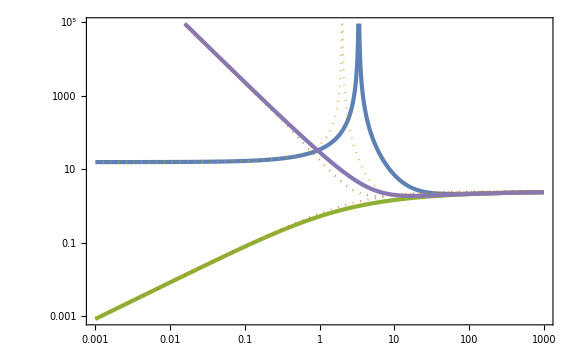

```mathematica
LogLogPlot[{fNLh[-η0,10],fNLCai[-η0,10],fNLh[-η0,10^-2],fNLCai[-η0,10^-2],fNLh[-η0,6],fNLCai[-η0,6]},{η0,10^-3,10^3},PlotStyle->{AbsoluteThickness[3],Dotted}]
```

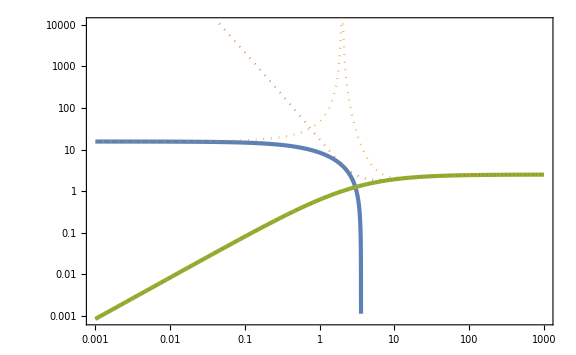

```mathematica
LogLogPlot[{fNLhapprox[-η0,10],fNLCai[-η0,10],fNLhapprox[-η0,10^-2],fNLCai[-η0,10^-2],fNLhapprox[-η0,6],fNLCai[-η0,6]},{η0,10^-3,10^3},PlotStyle->{AbsoluteThickness[3],Dotted}]
```

#### delta N

```mathematica
Quit[]
```

```mathematica
$Assumptions={H>0,Mpl>0,ϵ0>0,η0<0,3-4η0>0,s>3,dxL>0,δ>0,tc>tL,dotxL>0,dotxc>0};
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xSR[t_]=Simplify[Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-(√(2ϵ0))/Mpl V0+η0/Mpl^2 V0(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc],V0->3 Mpl^2 H^2}]/.{3-4η0->s^2/3,9-12η0->s^2}//Simplify
```

(dotxL ⅇ^(1/2 H (-(3+s) t+(-3+s) tc+6 tL)) (-1+ⅇ^(H s (t-tc))))/(H s)+xc-(ⅇ^(-1/2 H ((3+s) t-(-3+s) tc)) Mpl (ⅇ^(3 H tc) (-3+s)-2 ⅇ^(1/2 H ((3+s) t-(-3+s) tc)) s+ⅇ^(H (s (t-tc)+3 tc)) (3+s)) √ϵ0)/(√2 s η0)

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc+(dotxL ⅇ^(1/6 (-3 H (3+s) (t-tL)+(-3+s) Log[dotxL/(dotxL+3 H (dxL-xc+xL))])) (-1+ⅇ^(H s (t-tL)) (dotxL/(dotxL+3 H (dxL-xc+xL)))^(-s/3)))/(H s)-(ⅇ^(1/6 (-3 H (3+s) t+3 H (-3+s) tL+(-3+s) Log[dotxL/(dotxL+3 H (dxL-xc+xL))])) Mpl (-2 ⅇ^(1/2 H ((3+s) t-(-3+s) (tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)))) s+ⅇ^(H (s (t-tL)+3 tL)) (3+s) (dotxL/(dotxL+3 H (dxL-xc+xL)))^(1-s/3)+(dotxL ⅇ^(3 H tL) (-3+s))/(dotxL+3 H (dxL-xc+xL))) √ϵ0)/(√2 s η0)

```mathematica
xi0Eq={xbarSR[t+σ xi01+σ^2 xi02]==xSR[t]/.{dxL->σ dxL}/.{tc->tcUSR}};
```

```mathematica
xi0Eqlinear=Simplify[Normal[Series[xi0Eq,{σ,0,1}]]]/.{σ->1}//Simplify
```

{xi01 (-ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))+1/(dotxL+3 H (-xc+xL))dxL (-ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (-3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))==0}

```mathematica
xi0SR1[t_]=xi01/.Simplify[Solve[xi0Eqlinear[[1]],xi01][[1]]]
```

-((dxL (-ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (-3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0)))/((dotxL+3 H (-xc+xL)) (-ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))))

```mathematica
xi0Eqquad=Simplify[D[D[Normal[Series[xi0Eq,{σ,0,2}]], σ], σ]]
```

{(dotxL+3 H (-xc+xL)) (ⅇ^(H s (t-tL)) (-3+s) (H (-3+s) xi01^2+4 xi02) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+(3+s) (H (3+s) xi01^2-4 xi02) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))+2 dxL H (-9+s^2) xi01 (ⅇ^(H s (t-tL)) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+(dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))+(dxL^2 H (-9+s^2) (ⅇ^(H s (t-tL)) (√2 H Mpl (-9+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+(dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (9+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0)))/(dotxL+3 H (-xc+xL))==0}

```mathematica
xi0SR2[t_]=xi02/.Simplify[Solve[xi0Eqquad[[1]],xi02]][[1]]/.{xi01->xi0SR1[t]}//Simplify
```

(dxL^2 H (-((ⅇ^(H s (t-tL)) (-3+s)^2 (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0) (ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)-ⅇ^(H (3+s) t) (-3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))^2)/(ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)-ⅇ^(H (3+s) t) (3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))^2)-((3+s)^2 (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0) (ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)-ⅇ^(H (3+s) t) (-3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))^2)/(ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)-ⅇ^(H (3+s) t) (3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))^2+(2 (-9+s^2) (ⅇ^(H s (t-tL)) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+(dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0)) (-ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (-3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0)))/(-ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+ⅇ^(H (3+s) t) (3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))-(-9+s^2) (ⅇ^(H s (t-tL)) (√2 H Mpl (-9+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)+(dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (9+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0))))/(4 (dotxL+3 H (-xc+xL))^2 (ⅇ^(H s (t-tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxL η0+6 H (xc-xL) η0)-(3+s) (dotxL/(dotxL-3 H xc+3 H xL))^(s/3) (√2 H Mpl (-3+s) √ϵ0+2 dotxL η0+6 H (-xc+xL) η0)))

```mathematica
xi0SR[t_]=xi0SR1[t]+xi0SR2[t]/.{xc->xL+(dotxL-dotxc)/(3H)}/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

1/(4 dotxc^2)dxL (-(4 dotxc (-ⅇ^(H ((3+2 s) t-s tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxc η0)+ⅇ^(H (3+s) t+H s (tc-tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0+2 dotxc η0)))/(-ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxc η0)+ⅇ^(H (3+s) t+H s (tc-tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0+2 dotxc η0))+(dxL H ((2 ⅇ^(-H s tL) (-9+s^2) (ⅇ^(H s t) (√2 H Mpl (-3+s) √ϵ0-2 dotxc η0)+ⅇ^(H s tc) (√2 H Mpl (3+s) √ϵ0+2 dotxc η0)) (ⅇ^(H s t) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxc η0)-ⅇ^(H s tc) (-3+s) (√2 H Mpl (3+s) √ϵ0+2 dotxc η0)))/(ⅇ^(H s t) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxc η0)-ⅇ^(H s tc) (3+s) (√2 H Mpl (-3+s) √ϵ0+2 dotxc η0))-(ⅇ^(H s (t-tL)) (-3+s)^2 (√2 H Mpl (3+s) √ϵ0-2 dotxc η0) (ⅇ^(H s t) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxc η0)-ⅇ^(H s tc) (-3+s) (√2 H Mpl (3+s) √ϵ0+2 dotxc η0))^2)/((ⅇ^(H s t) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxc η0)-ⅇ^(H s tc) (3+s) (√2 H Mpl (-3+s) √ϵ0+2 dotxc η0))^2)-(ⅇ^(H s (tc-tL)) (3+s)^2 (√2 H Mpl (-3+s) √ϵ0+2 dotxc η0) (ⅇ^(H s t) (3+s) (√2 H Mpl (-3+s) √ϵ0-2 dotxc η0)-ⅇ^(H s tc) (-3+s) (√2 H Mpl (3+s) √ϵ0+2 dotxc η0))^2)/((ⅇ^(H s t) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxc η0)-ⅇ^(H s tc) (3+s) (√2 H Mpl (-3+s) √ϵ0+2 dotxc η0))^2)-(-9+s^2) (ⅇ^(H s (t-tL)) (√2 H Mpl (-9+s) √ϵ0-2 dotxc η0)+ⅇ^(H s (tc-tL)) (√2 H Mpl (9+s) √ϵ0+2 dotxc η0))))/(ⅇ^(H s (t-tL)) (-3+s) (√2 H Mpl (3+s) √ϵ0-2 dotxc η0)-ⅇ^(H s (tc-tL)) (3+s) (√2 H Mpl (-3+s) √ϵ0+2 dotxc η0)))

```mathematica
fNL[t_]=5/6(H D[D[xi0SR[t], dxL], dxL])/(H D[xi0SR[t], dxL])^2/.{dotxc->δ √(2ϵ0)Mpl H}/.{dxL->0}//Simplify
```

(5 (ⅇ^(H ((3+2 s) t-s tL)) (-3+s) (3+s-2 δ η0)-ⅇ^(H (3+s) t+H s (tc-tL)) (3+s) (-3+s+2 δ η0))^2 ((2 ⅇ^(-H s tL) (-9+s^2) (ⅇ^(H s t) (-3+s-2 δ η0)+ⅇ^(H s tc) (3+s+2 δ η0)) (ⅇ^(H s t) (3+s) (-3+s-2 δ η0)-ⅇ^(H s tc) (-3+s) (3+s+2 δ η0)))/(ⅇ^(H s t) (-3+s) (3+s-2 δ η0)-ⅇ^(H s tc) (3+s) (-3+s+2 δ η0))-(ⅇ^(H s (t-tL)) (-3+s)^2 (3+s-2 δ η0) (ⅇ^(H s t) (3+s) (-3+s-2 δ η0)-ⅇ^(H s tc) (-3+s) (3+s+2 δ η0))^2)/((ⅇ^(H s t) (-3+s) (3+s-2 δ η0)-ⅇ^(H s tc) (3+s) (-3+s+2 δ η0))^2)-(ⅇ^(H s (tc-tL)) (3+s)^2 (-3+s+2 δ η0) (ⅇ^(H s t) (3+s) (-3+s-2 δ η0)-ⅇ^(H s tc) (-3+s) (3+s+2 δ η0))^2)/((ⅇ^(H s t) (-3+s) (3+s-2 δ η0)-ⅇ^(H s tc) (3+s) (-3+s+2 δ η0))^2)-(-9+s^2) (ⅇ^(H s (t-tL)) (-9+s-2 δ η0)+ⅇ^(H s (tc-tL)) (9+s+2 δ η0))))/(12 (ⅇ^(H s (t-tL)) (-3+s) (3+s-2 δ η0)-ⅇ^(H s (tc-tL)) (3+s) (-3+s+2 δ η0)) (ⅇ^(H ((3+2 s) t-s tL)) (3+s) (-3+s-2 δ η0)-ⅇ^(H (3+s) t+H s (tc-tL)) (-3+s) (3+s+2 δ η0))^2)

```mathematica
fNLLim=Limit[fNL[t],{t->∞}]//FullSimplify
```

(5 (-3+s) (-9+12 δ η0+(s-2 δ η0)^2))/(2 (3+s) (-3+s-2 δ η0)^2)

```mathematica
fNLLim/.{δ->-h/6}//Simplify
```

(5 (-3+s) (-9-2 h η0+(s+(h η0)/3)^2))/(2 (3+s) (-3+s+(h η0)/3)^2)

#### Cai

```mathematica
Quit[]
```

```mathematica
$Assumptions={H>0,Mpl>0,ϵ0>0,η0<0,3-4η0>0,s>3,dxL>0,δ>0,tc>tL,dotxL>0,dotxc>0};
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xSR[t_]=(s-3-h)/(s(s-3))pie Exp[1/2(s-3)H(t-tc)]+(2pie h)/(s^2-9)+xc/.{h->-6Sqrt[2ϵ0]Mpl/pie}/.{pie->xUSR'[tc]/H}
```

xc+(dotxL ⅇ^(1/2 H (-3+s) (t-tc)+3 H (-tc+tL)) (-3+s+(6 √2 ⅇ^(-3 H (-tc+tL)) H Mpl √ϵ0)/dotxL))/(H (-3+s) s)-(12 √2 Mpl √ϵ0)/(-9+s^2)

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc+(ⅇ^(1/6 (-3+s) (3 H (t-tL)-Log[dotxL/(dotxL+3 H (dxL-xc+xL))])) (dotxL (-3+s)+3 H (dxL (-3+s)+3 xc-s xc-3 xL+s xL+2 √2 Mpl √ϵ0)))/(H (-3+s) s)-(12 √2 Mpl √ϵ0)/(-9+s^2)

```mathematica
xi0Eq={xbarSR[t+σ xi01+σ^2 xi02]==xSR[t]/.{dxL->σ dxL}/.{tc->tcUSR}};
```

```mathematica
xi0Eqlinear=Simplify[Normal[Series[xi0Eq,{σ,0,1}]]]/.{σ->1}//Simplify
```

{1/(dotxL+3 H (-xc+xL))(dotxL dxL (3+s)+dotxL^2 (-3+s) xi01+9 H^2 xi01 (xc-xL) ((-3+s) xc-(-3+s) xL-2 √2 Mpl √ϵ0)-3 dxL H ((3+s) xc-(3+s) xL-2 √2 Mpl √ϵ0)+6 dotxL H xi01 (-(-3+s) xc+(-3+s) xL+√2 Mpl √ϵ0))==0}

```mathematica
xi0SR1[t_]=xi01/.Simplify[Solve[xi0Eqlinear[[1]],xi01][[1]]]
```

-(dxL (dotxL (3+s)+3 H (-(3+s) xc+(3+s) xL+2 √2 Mpl √ϵ0)))/((dotxL+3 H (-xc+xL)) (dotxL (-3+s)+3 H (-(-3+s) xc+(-3+s) xL+2 √2 Mpl √ϵ0)))

```mathematica
xi0Eqquad=Simplify[D[D[Normal[Series[xi0Eq,{σ,0,2}]], σ], σ]]
```

{1/((-3+s) s)ⅇ^(1/6 (-3+s) (3 H (t-tL)-Log[dotxL/(dotxL+3 H (-xc+xL))])) (3 dxL H (-3+s)^2 (xi01+dxL/(dotxL+3 H (-xc+xL)))+1/4 (-3+s) (4 xi02-(6 dxL^2 H)/(dotxL+3 H (-xc+xL))^2+H (-3+s) (xi01+dxL/(dotxL+3 H (-xc+xL)))^2) (dotxL (-3+s)+3 H (-(-3+s) xc+(-3+s) xL+2 √2 Mpl √ϵ0)))==0}

```mathematica
xi0SR2[t_]=xi02/.Simplify[Solve[xi0Eqquad[[1]],xi02]][[1]]/.{xi01->xi0SR1[t]}//Simplify
```

(3 dxL^2 H (dotxL^2 (-9+s^2)-6 dotxL H (-3+s) ((3+s) xc-(3+s) xL-2 √2 Mpl √ϵ0)+9 H^2 ((-9+s^2) xc^2+(-9+s^2) xL^2-2 (-3+s) xc ((3+s) xL+2 √2 Mpl √ϵ0)+4 √2 Mpl (-3+s) xL √ϵ0+8 Mpl^2 ϵ0)))/(2 (dotxL+3 H (-xc+xL))^2 (dotxL (-3+s)+3 H (-(-3+s) xc+(-3+s) xL+2 √2 Mpl √ϵ0))^2)

```mathematica
xi0SR[t_]=xi0SR1[t]+xi0SR2[t]/.{xc->xL+(dotxL-dotxc)/(3H)}/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(dxL (-2 dotxc^3 (-9+s^2)+3 dotxc^2 H (dxL (-9+s^2)-8 √2 Mpl s √ϵ0)+36 dotxc H^2 Mpl (√2 dxL (-3+s)-4 Mpl √ϵ0) √ϵ0+216 dxL H^3 Mpl^2 ϵ0))/(2 dotxc^2 (dotxc (-3+s)+6 √2 H Mpl √ϵ0)^2)

```mathematica
fNL[t_]=5/6(H D[D[xi0SR[t], dxL], dxL])/(H D[xi0SR[t], dxL])^2/.{dotxc->δ √(2ϵ0)Mpl H}/.{dxL->0}/.{δ->-6/h,s->3-2η0}//Simplify
```

(5 (h^2+4 h η0+4 (-3+η0) η0))/(2 (-6+h+2 η0)^2)

#### Cai in Suyama formula

```mathematica
Quit[]
```

```mathematica
$Assumptions={H>0,Mpl>0,ϵ0>0,η0<0,3-4η0>0,s>3,dxL>0,δ>0,tc>tL,dotxL>0,dotxc>0};
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xSR[t_]=(s-3-h)/(s(s-3))pie Exp[1/2(s-3)H(t-tc)]+(2pie h)/(s^2-9)+xc/.{h->-6Sqrt[2ϵ0]Mpl/pie}/.{pie->xUSR'[tc]/H}
```

xc+(dotxL ⅇ^(1/2 H (-3+s) (t-tc)+3 H (-tc+tL)) (-3+s+(6 √2 ⅇ^(-3 H (-tc+tL)) H Mpl √ϵ0)/dotxL))/(H (-3+s) s)-(12 √2 Mpl √ϵ0)/(-9+s^2)

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc+(ⅇ^(1/6 (-3+s) (3 H (t-tL)-Log[dotxL/(dotxL+3 H (dxL-xc+xL))])) (dotxL (-3+s)+3 H (dxL (-3+s)+3 xc-s xc-3 xL+s xL+2 √2 Mpl √ϵ0)))/(H (-3+s) s)-(12 √2 Mpl √ϵ0)/(-9+s^2)

```mathematica
xi0Eq={xbarSR[t+σ xi0]==xSR[t]/.{dxL->σ dxL}/.{tc->tcUSR}};
```

```mathematica
xi0Eqlinear=Simplify[Normal[Series[xi0Eq,{σ,0,1}]]]/.{σ->1}//Simplify
```

{1/(dotxL+3 H (-xc+xL))(dotxL dxL (3+s)+dotxL^2 (-3+s) xi0+9 H^2 xi0 (xc-xL) ((-3+s) xc-(-3+s) xL-2 √2 Mpl √ϵ0)-3 dxL H ((3+s) xc-(3+s) xL-2 √2 Mpl √ϵ0)+6 dotxL H xi0 (-(-3+s) xc+(-3+s) xL+√2 Mpl √ϵ0))==0}

```mathematica
xi0SR[t_]=Collect[xi0/.Simplify[Simplify[Solve[xi0Eqlinear[[1]],xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxL->dotxc Exp[3H(tc-tL)]},dxL,Simplify]
```

-(dxL (dotxc (3+s)+6 √2 H Mpl √ϵ0))/(dotxc (dotxc (-3+s)+6 √2 H Mpl √ϵ0))

```mathematica
xi0δ[t_,δ_]=xi0SR[t]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

-(dxL (6+(3+s) δ))/(√2 H Mpl δ (6+(-3+s) δ) √ϵ0)

```mathematica
powern[t_]=-δ/xi0δ[t,δ]^2 D[(xi0δ[t,δ]^2), δ]//Simplify
```

(72+24 (-3+s) δ+2 (-9+s^2) δ^2)/((6+(-3+s) δ) (6+(3+s) δ))

```mathematica
Coeff[t]=Collect[xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,dxL,Simplify]
```

-(dxL ⅇ^(1/2 H (-3+s) (t-tc)) H (-3+s) (6+(3+s) δ))/(4 s δ)

```mathematica
Correction[t_]=Coeff[t]/(xSR''[t]xi0SR[t])/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

1

```mathematica
Zcintegrand[t_]=Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

(2 ⅇ^(H s (-t+tc)) s^2)/(H^2 Mpl^2 (6+(-3+s) δ)^2 ϵ0)

```mathematica
Zcint[t_]=Integrate[Zcintegrand[t],t]//Simplify
```

-(2 ⅇ^(H s (-t+tc)) s)/(H^3 Mpl^2 (6+(-3+s) δ)^2 ϵ0)

```mathematica
Zc[t_]=1+3H dotxc^2(Zcint[t]-Zcint[tc]+Exp[-3H (t-tc)]/(xSR''[t]xSR'[t]))/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

1-(12 (-1+ⅇ^(H s (-t+tc))) s δ^2)/(6+(-3+s) δ)^2+(24 ⅇ^(H s (-t+tc)) s^2 δ^2)/((-3+s) (6+(-3+s) δ)^2)

```mathematica
fNL[t_]=Correction[t](5powern[t])/(4Zc[t])//Simplify
```

(5 (-3+s) (6+(-3+s) δ) (36+12 (-3+s) δ+(-9+s^2) δ^2))/(2 (6+(3+s) δ) (-27 (-2+δ)^2+s^3 δ^2+3 s^2 δ (4+δ+4 ⅇ^(H s (-t+tc)) δ)+9 s (4-8 δ+(-1+4 ⅇ^(H s (-t+tc))) δ^2)))

```mathematica
fNLLim=Limit[fNL[t],{t->∞}]//FullSimplify
```

(5 (6+(-3+s) δ) (36+(-3+s) δ (12+(3+s) δ)))/(2 (6+(3+s) δ) (36+12 (-3+s) δ+(3+s)^2 δ^2))

```mathematica
Normal[Series[fNLLim/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify
```

5/(2 (1+δ) (1+δ^2))

```mathematica
Series[fNLLim/.{s->Sqrt[9-12η0]},{η0,0,2}]//Simplify
```

5/(2 (1+δ) (1+δ^2))-(5 (δ^3 (1+4 δ+δ^2)) η0)/(6 ((1+δ)^2 (1+δ^2)^2))+(5 δ^4 (-3-13 δ-18 δ^2-12 δ^3+δ^4+δ^5) η0^2)/(18 (1+δ)^3 (1+δ^2)^3)+O[η0]^3

```mathematica
fNLLim/.{δ->-6/h,s->3-2η0}//Simplify
```

(5 (h+2 η0) (h^2+4 h η0+4 (-3+η0) η0))/(2 (-6+h+2 η0) (h^2+4 (-3+η0)^2+4 h η0))

```mathematica
LimCor=Limit[Correction[t],{t->∞}]
Limn=Limit[powern[t],{t->∞}]//Simplify
LimZc=Limit[Zc[t],{t->∞}]//Simplify
```

1

(72+24 (-3+s) δ+2 (-9+s^2) δ^2)/((6+(-3+s) δ) (6+(3+s) δ))

1+(12 s δ^2)/(6+(-3+s) δ)^2

```mathematica
LimCor (5Limn)/(4LimZc)//FullSimplify
```

(5 (6+(-3+s) δ) (36+(-3+s) δ (12+(3+s) δ)))/(2 (6+(3+s) δ) (36+12 (-3+s) δ+(3+s)^2 δ^2))

```mathematica
LimCor/.{η0->0}
Normal[Series[Limn/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify
Normal[Series[LimZc/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify
```

1

2/(1+δ)

1+δ^2

```mathematica
Limit[Normal[Series[Correction[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify,{t->∞}]
Limit[Normal[Series[powern[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify,{t->∞}]
Limit[Normal[Series[Zc[t]/.{s->Sqrt[9-12η0]},{η0,0,0}]]//Simplify,{t->∞}]
```

1

2/(1+δ)

1+δ^2

### Motohashi

```mathematica
Quit[]
```

```mathematica
$Assumptions={V0>0,Mpl>0,dx>0,ϵSR>0,x1∈Reals}
```

{V0>0,Mpl>0,dx>0,ϵSR>0,x1∈ℝ}

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/(2Mpl)(1+Tanh[(x-x1)/dx]);
```

```mathematica
Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify
```

(V0 √ϵSR (-x1+dx Log[2]))/(√2 Mpl)

```mathematica
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//FullSimplify
```

V0-(V0 √ϵSR (x-x1+dx Log[2 Cosh[(x-x1)/dx]]))/(√2 Mpl)

```mathematica
Limit[V[x],{x->-∞}]
```

V0

```mathematica
V'[x]-Vp[x]
```

0

```mathematica
Limit[Mpl^2/2(V'[x]/V0)^2//Simplify,{x->∞}]
```

ϵSR

#### dNS=5e-3 practice

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
```

```mathematica
Limit[Integrate[Vp[x],x],{x->-∞}]
```

(dx V0 √ϵSR Log[2])/(√2)

```mathematica
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify
```

V0-(dx V0 √ϵSR Log[2])/(√2)-(V0 √ϵSR (x+dx Log[Cosh[x/dx]]))/(√2)

```mathematica
Limit[V[x],{x->-∞}]
```

V0

```mathematica
V'[x]-Vp[x]//Simplify
```

0

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=5 10^-3;
```

```mathematica
deltas=10^-3;
```

```mathematica
V0s=3 Hs^2;V0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
ϵSRs=deltas^-2 ϵUSRcs;ϵSRs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[ϵUSRi/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

3.×10^-8

1.26651×10^-8

0.0126651

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNi=10^-1 dNs;
dxs=dotxcs dNi/Hs;dxs//N
```

7.95775×10^-8

```mathematica
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
```

```mathematica
tf=2NLs/Hs;tf//N
```

45264.1

```mathematica
x2m=2dxs;x2m//N
```

1.59155×10^-7

```mathematica
dotxUSR[t_]=dotxL Exp[-3 √(V0/3) t];
```

```mathematica
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];//AbsoluteTiming
```

{58.4766,Null}

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hsol[t] dotxsol[t])/.params;
```

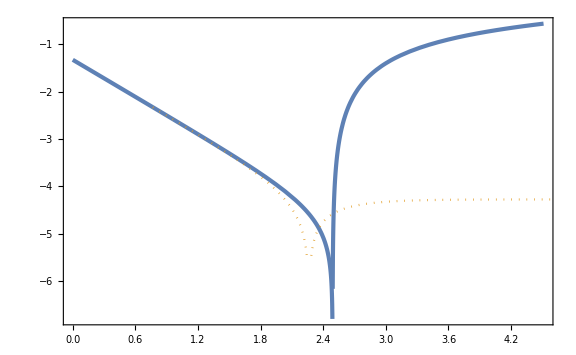

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[Abs[xsol[t]]]},{t,0,tf},PlotRange->Full],Plot[Log10[Abs[xLs+dotxLs/(3Hs)(1-Exp[-3NN])]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

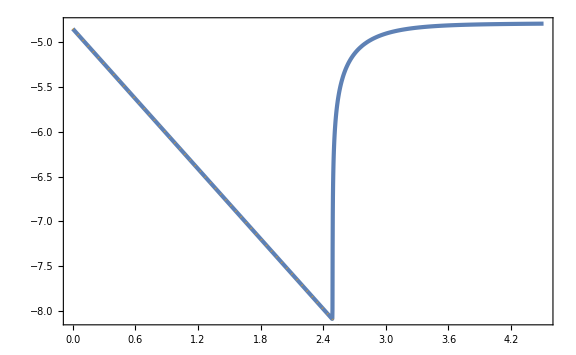

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[dotxsol[t]]},{t,0,tf},PlotRange->Full],Plot[Log10[dotxLs Exp[-3NN]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

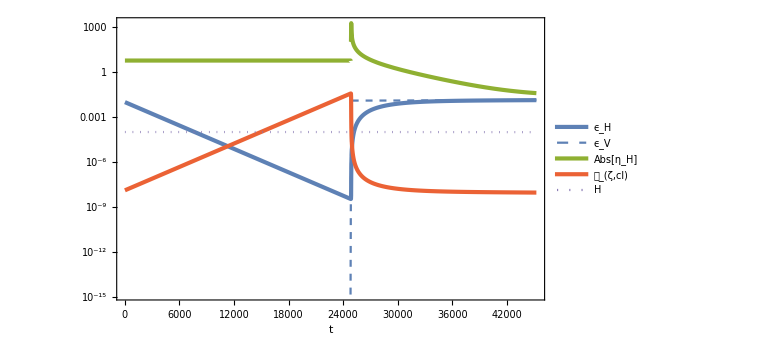

```mathematica
LogPlot[{ϵsol[t],ϵVsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hsol[t]/(2π))^2,Hsol[t]},{t,0,tf},PlotLegends->{Subscript[ϵ, H],Subscript[ϵ, V],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl],H},FrameLabel->{t,None},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},AbsoluteThickness[3],AbsoluteThickness[3],Dotted}]
```

```mathematica
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]
```

24893.1558368661042698174773401

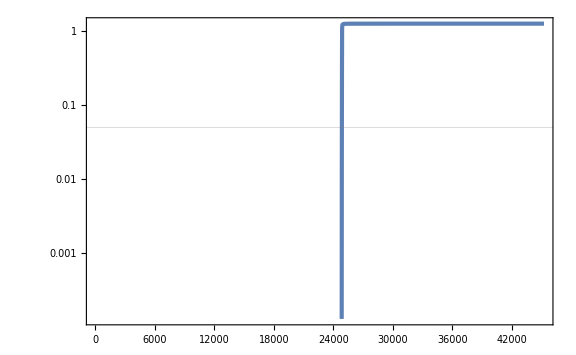

```mathematica
LogPlot[(1-dotxUSR[t]/dotxsol[t])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,0,tf},GridLines->{None,{0.05}},PlotRange->Full]
```

```mathematica
t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function (1-ⅇ^(-3 t/10000)/(50000 √2 InterpolatingFunction[{{0,45264.1389511827300420350562861}},{5,3,2,{449},{4},{1},0,0,0,Automatic,{},{},False},{{0,«49»,«399»}},{«1»},{Automatic}][t])==0.0398684648936185488507055) is less than WorkingPrecision (30.).

24872.094869088261693709981221

```mathematica
(1-dotxUSR[t2p]/dotxsol[t2p])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params
```

0.05

```mathematica
x2p=xsol[t2p]
```

-1.6661319702168365779091874×10^-7

```mathematica
dN=Nsol[t2m]-Nsol[t2p]
```

0.002106096778925584179493352

```mathematica
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p];
{dNi,dN},{logdNi,Log10[dNs]-1,Log10[dNs]+1,1/10}];//AbsoluteTiming
Clear[dNi]
```

{36.1901,Null}

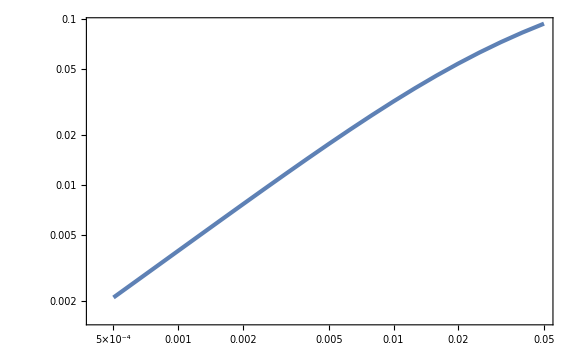

```mathematica
ListLogLogPlot[dNsList]
```

```mathematica
dNsint[dNi_]=Interpolation[dNsList][dNi];
```

```mathematica
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs},WorkingPrecision->30]
```

0.00126027625726377094846909520944

```mathematica
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]
```

0.0049999974801499393272103825

```mathematica
deltaM=√(ϵsol[t2p]/ϵVsol[t2m])
```

0.000550466323462724140936847

```mathematica
deltaeff=((dN/1.5)^3+deltaM^3)^(1/3)
```

0.00333833

```mathematica
fNLM=5/2 1/(1+deltaeff)^2
```

2.48339

```mathematica
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}]
xc=xsol[tc]
```

9997.23

-0.00232008

```mathematica
Neval=Nsol[tf]-1
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]
```

3.5106851214297895637367993435

FindRoot::precw: The precision of the argument function (InterpolatingFunction[{{0,45264.1389511827300420350562861}},{5,3,1,{473},{4},0,0,0,0,Automatic,{},{},False},{{0,«49»,«423»}},{{0,0.000100166528008778128624246004569},{5.0764718919540190056223453471×10^-8,0.000100166527958097818200408657717},«48»,«423»},{Automatic}][t]==«77») is less than WorkingPrecision (30.).

0.1128617482702069523629916025

```mathematica
tS=tc;
```

```mathematica
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];//AbsoluteTiming
```

{26.0761,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(3.0137072824207485445127246×10^-14)/x^2

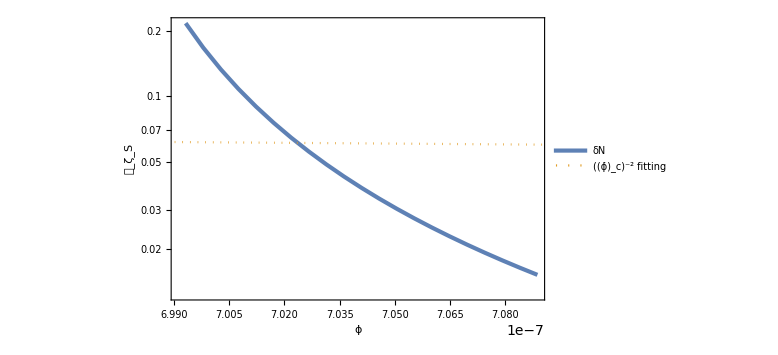

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-7,3 10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

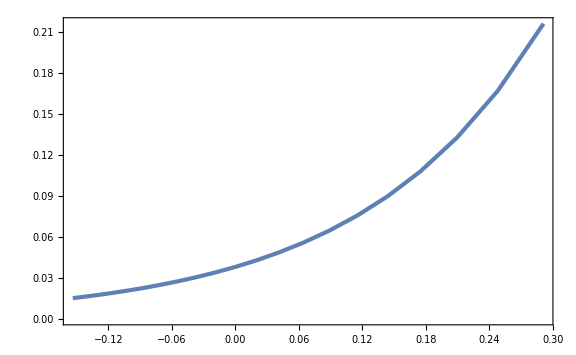

```mathematica
ListPlot[PSvszetaL]
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.038068857603646448135907657

```mathematica
fNLdN=5/12 PSvszetaLint'[0]/PS0
```

2.4860688936244307808507

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30]
dotxc=dotxsol[tc]
```

9997.23257342910069996027235966

7.040954731396723655584439×10^-7

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

171.606321025341976196

```mathematica
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;//AbsoluteTiming
Zc
```

{0.888962,Null}

86.220406527929418718948253

```mathematica
fNLM
fNLdN
fNLS=(5power)/(4Zc)
```

2.48339

2.4860688936244307808507

2.487901761541704401675

#### dNS=5e-3

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify;
dotxUSR[NN_]=dotxL Exp[-3NN];
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=5 10^-3;
V0s=3 Hs^2;
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];
NLs=1/6 Log[ϵUSRi/ϵUSRcs];
dotxLs=dotxcs Exp[3 NLs];
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;
tf=2NLs/Hs;
```

```mathematica
fNLList=ParallelTable[
deltas=10^logdeltas;
ϵSRs=deltas^-2 ϵUSRcs;
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p];
{dNi,dN},{logdNi,Log10[dNs]-1,Log10[dNs]+1,1/10}];
Clear[dNi];
dNsint[dNi_]=Interpolation[dNsList][dNi];
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs},WorkingPrecision->30];
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;
dN=Nsol[t2m]-Nsol[t2p];
deltaM=√(ϵsol[t2p]/ϵVsol[t2m]);
deltaeff=((dN/1.5)^3+deltaM^3)^(1/3);
fNLM=5/2 1/(1+deltaeff)^2;
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}];
xc=xsol[tc];
Neval=Nsol[tf]-1;
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]//Quiet;
tS=tc;
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
PS0=PSvszetaLint[0];
fNLdN=5/12 PSvszetaLint'[0]/PS0;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30];
dotxc=dotxsol[tc];
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc];
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;
fNLS=(5power)/(4Zc);
{deltaM,deltaeff,power,Zc,fNLM,fNLdN,fNLS},{logdeltas,-3,0,1/10}];//AbsoluteTiming
```

{338.674,Null}

```mathematica
SetDirectory["~/Documents/Univ/LOE_beyond_fNL"];
```

```mathematica
Export["fNLList_dN=5e-3.dat",fNLList];
```

```mathematica
fNLMvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,1,0,0}}];
fNLdNvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,1,0}}];
fNLSvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
```

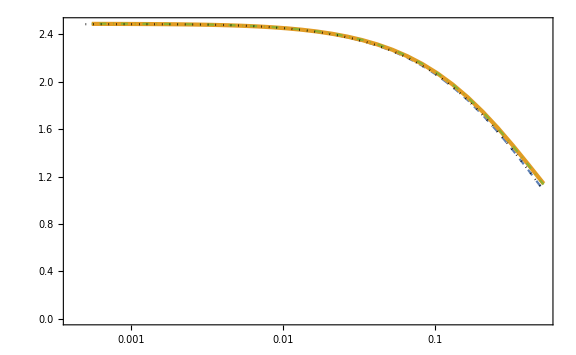

```mathematica
Show[ListLogLinearPlot[{fNLMvsdM,fNLdNvsdM,fNLSvsdM},PlotStyle->{Dashed,AbsoluteThickness[3],DotDashed}],LogLinearPlot[5/2 1/((1+((dNs/1.5)^3+dM^3)^(1/3))^2),{dM,5 10^-4,0.5},PlotStyle->{Black,Dotted}]]
```

#### dNS=5e-2 practice

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
```

```mathematica
Limit[Integrate[Vp[x],x],{x->-∞}]
```

(dx V0 √ϵSR Log[2])/(√2)

```mathematica
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify
```

V0-(dx V0 √ϵSR Log[2])/(√2)-(V0 √ϵSR (x+dx Log[Cosh[x/dx]]))/(√2)

```mathematica
Limit[V[x],{x->-∞}]
```

V0

```mathematica
V'[x]-Vp[x]//Simplify
```

0

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=5 10^-2;
```

```mathematica
deltas=10^0;
```

```mathematica
V0s=3 Hs^2;V0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
ϵSRs=deltas^-2 ϵUSRcs;ϵSRs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[ϵUSRi/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

3.×10^-8

1.26651×10^-8

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNi=10^-1 dNs;
dxs=dotxcs dNi/Hs;dxs//N
```

7.95775×10^-7

```mathematica
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
```

```mathematica
tf=2NLs/Hs;tf//N
```

45264.1

```mathematica
x2m=2dxs;x2m//N
```

1.59155×10^-6

```mathematica
dotxUSR[t_]=dotxL Exp[-3 √(V0/3) t];
```

```mathematica
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];//AbsoluteTiming
```

{0.255825,Null}

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hsol[t] dotxsol[t])/.params;
```

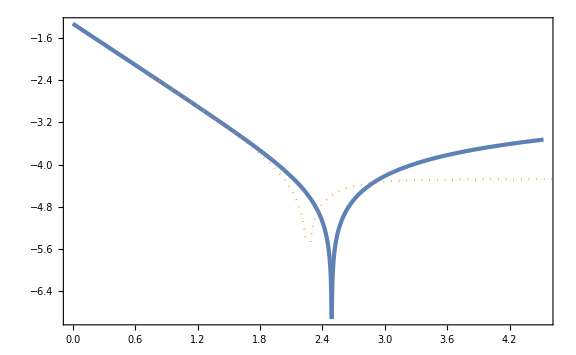

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[Abs[xsol[t]]]},{t,0,tf},PlotRange->Full],Plot[Log10[Abs[xLs+dotxLs/(3Hs)(1-Exp[-3NN])]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

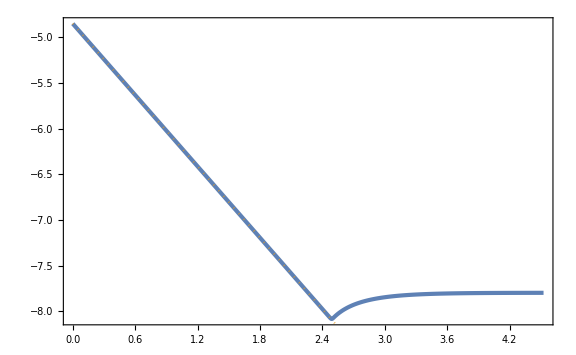

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[dotxsol[t]]},{t,0,tf},PlotRange->Full],Plot[Log10[dotxLs Exp[-3NN]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

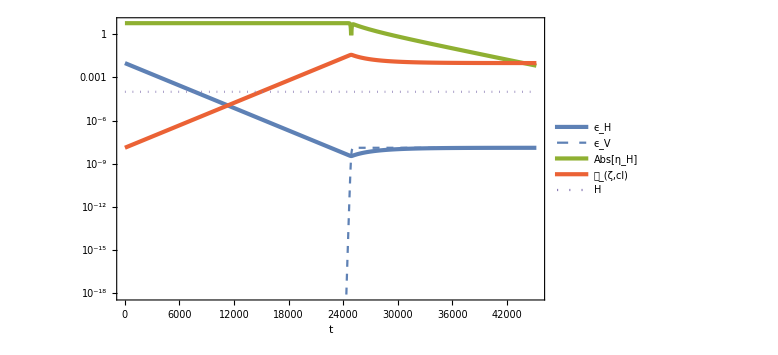

```mathematica
LogPlot[{ϵsol[t],ϵVsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hsol[t]/(2π))^2,Hsol[t]},{t,0,tf},PlotLegends->{Subscript[ϵ, H],Subscript[ϵ, V],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl],H},FrameLabel->{t,None},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},AbsoluteThickness[3],AbsoluteThickness[3],Dotted}]
```

```mathematica
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]
```

25082.7351258537071911145986665

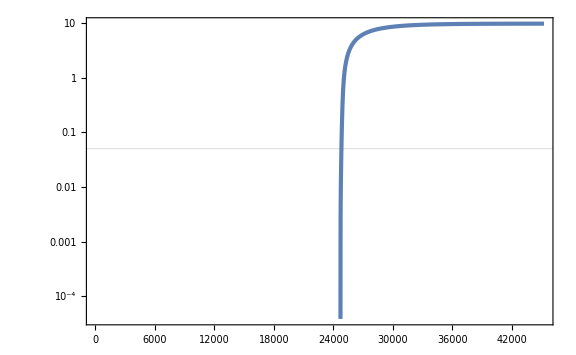

```mathematica
LogPlot[(1-dotxUSR[t]/dotxsol[t])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,0,tf},GridLines->{None,{0.05}},PlotRange->Full]
```

```mathematica
t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function (1-ⅇ^(-3 t/10000)/(50000 √2 InterpolatingFunction[{{0,45264.1389511827300420350562861}},{5,3,2,{479},{4},{1},0,0,0,Automatic,{},{},False},{{0,«49»,«429»}},{«1»},{Automatic}][t])==0.005162541775976105716780742) is less than WorkingPrecision (30.).

24824.7449130037636102895992965

```mathematica
(1-dotxUSR[t2p]/dotxsol[t2p])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params
```

0.05

```mathematica
x2p=xsol[t2p]
```

-5.530958302377843919639224×10^-7

```mathematica
dN=Nsol[t2m]-Nsol[t2p]
```

0.0257990212984383857196602175

```mathematica
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-dNi/Hs},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p];
{dNi,dN},{logdNi,Log10[dNs]-1,Log10[dNs]+1,1/10}];//AbsoluteTiming
Clear[dNi]
```

{2.61096,Null}

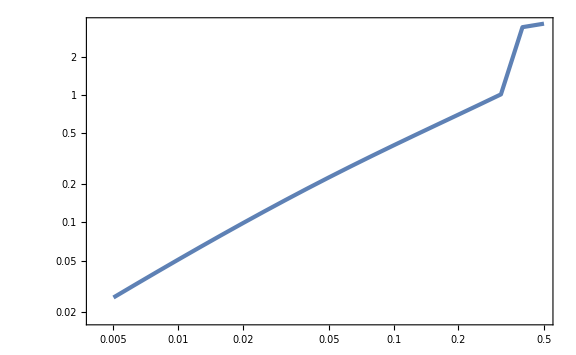

```mathematica
ListLogLogPlot[dNsList]
```

```mathematica
dNsint[dNi_]=Interpolation[dNsList][dNi];
```

```mathematica
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs},WorkingPrecision->30]
```

InterpolatingFunction::dmval: Input value {0.00485364633889573755040349335155} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.00976703497758747936424271635671

```mathematica
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]
```

0.0499999959644867422449949669

```mathematica
deltaM=√(ϵsol[t2p]/ϵVsol[t2m])
```

0.5440854841778355776261207

```mathematica
deltaeff=((dN/1.5)^3+deltaM^3)^(1/3)
```

0.544127

```mathematica
fNLM=5/2 1/(1+deltaeff)^2
```

1.04851

```mathematica
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}]
xc=xsol[tc]
```

9997.23

-0.00232008

```mathematica
Neval=Nsol[tf]-1
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]
```

3.5266913071762679669036556786

FindRoot::precw: The precision of the argument function (InterpolatingFunction[{{0,45264.1389511827300420350562861}},{5,3,1,{467},{4},0,0,0,0,Automatic,{},{},False},{{0,«49»,«417»}},{{0,0.000100166528008778128624246004569},{5.0764718919540190056223453471×10^-8,0.000100166527958097818200408657717},«48»,«417»},{Automatic}][t]==«79») is less than WorkingPrecision (30.).

0.0001401369730624748079183342875

```mathematica
tS=tc;
```

```mathematica
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];//AbsoluteTiming
```

{4.88827,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(5.7373285488803576565630483×10^-14)/x^2

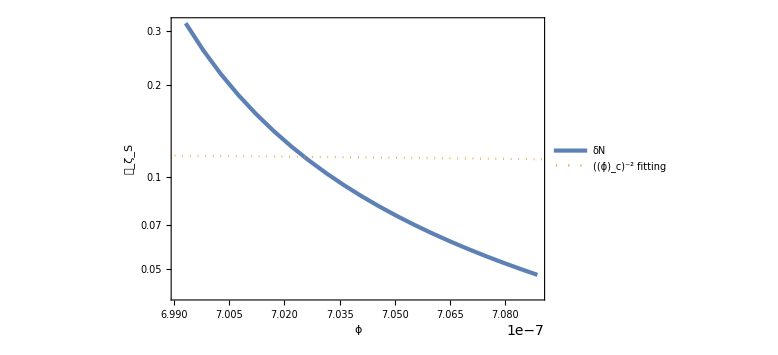

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-7,3 10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

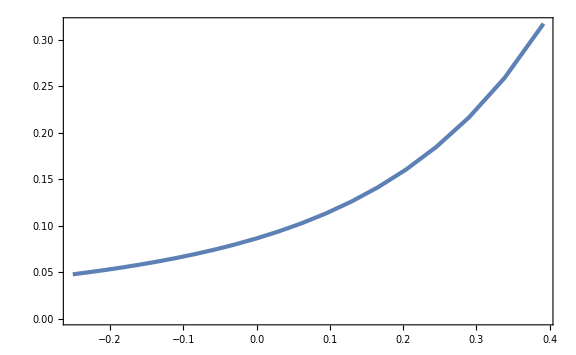

```mathematica
ListPlot[PSvszetaL]
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.0866047125754002069030962026

```mathematica
fNLdN=5/12 PSvszetaLint'[0]/PS0
```

1.12715632990394455126684

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30]
dotxc=dotxsol[tc]
```

9997.23257342910069996027235966

7.040954731396723655584439×10^-7

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

117.368128940980611121

```mathematica
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;//AbsoluteTiming
Zc
```

{0.896326,Null}

131.06618069387565050200403

```mathematica
fNLM
fNLdN
fNLS=(5power)/(4Zc)
```

1.04851

1.12715632990394455126684

1.119359398431613198531

#### dNS=5e-2

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify;
dotxUSR[NN_]=dotxL Exp[-3NN];
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=5 10^-2;
V0s=3 Hs^2;
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];
NLs=1/6 Log[ϵUSRi/ϵUSRcs];
dotxLs=dotxcs Exp[3 NLs];
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;
tf=2NLs/Hs;
```

```mathematica
fNLList=ParallelTable[
deltas=10^logdeltas;
ϵSRs=deltas^-2 ϵUSRcs;
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m-dNi/Hs},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p];
{dNi,dN},{logdNi,Log10[dNs]-1,Log10[dNs]+1,1/10}];
Clear[dNi];
dNsint[dNi_]=Interpolation[dNsList][dNi];
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs},WorkingPrecision->30]//Quiet;
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;
dN=Nsol[t2m]-Nsol[t2p];
deltaM=√(ϵsol[t2p]/ϵVsol[t2m]);
deltaeff=((dN/1.5)^3+deltaM^3)^(1/3);
fNLM=5/2 1/(1+deltaeff)^2;
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}];
xc=xsol[tc];
Neval=Nsol[tf]-1;
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]//Quiet;
tS=tc;
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
PS0=PSvszetaLint[0];
fNLdN=5/12 PSvszetaLint'[0]/PS0;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30];
dotxc=dotxsol[tc];
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc];
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;
fNLS=(5power)/(4Zc);
{deltaM,deltaeff,power,Zc,fNLM,fNLdN,fNLS},{logdeltas,-3,0,1/10}];//AbsoluteTiming
```

{69.9046,Null}

```mathematica
SetDirectory["~/Documents/Univ/LOE_beyond_fNL"];
```

```mathematica
Export["fNLList_dN=5e-2.dat",fNLList];
```

```mathematica
fNLMvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,1,0,0}}];
fNLdNvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,1,0}}];
fNLSvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
```

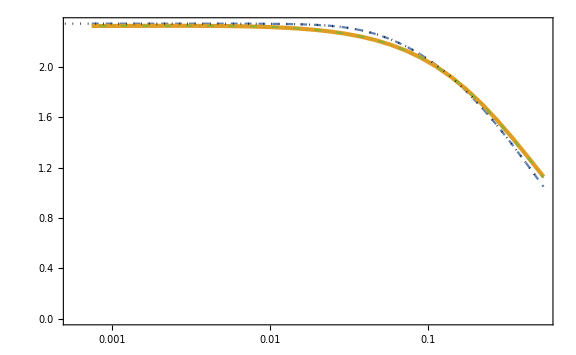

```mathematica
Show[ListLogLinearPlot[{fNLMvsdM,fNLdNvsdM,fNLSvsdM},PlotStyle->{Dashed,AbsoluteThickness[3],DotDashed}],LogLinearPlot[5/2 1/((1+((dNs/1.5)^3+dM^3)^(1/3))^2),{dM,5 10^-4,0.5},PlotStyle->{Black,Dotted}]]
```

#### dNS=0.1 practice

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
```

```mathematica
Limit[Integrate[Vp[x],x],{x->-∞}]
```

(dx V0 √ϵSR Log[2])/(√2)

```mathematica
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify
```

V0-(dx V0 √ϵSR Log[2])/(√2)-(V0 √ϵSR (x+dx Log[Cosh[x/dx]]))/(√2)

```mathematica
Limit[V[x],{x->-∞}]
```

V0

```mathematica
V'[x]-Vp[x]//Simplify
```

0

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=1/10;
```

```mathematica
deltas=10^0;
```

```mathematica
V0s=3 Hs^2;V0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
ϵSRs=deltas^-2 ϵUSRcs;ϵSRs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[ϵUSRi/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

3.×10^-8

1.26651×10^-8

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNi=10^-1 dNs;
dxs=dotxcs dNi/Hs;dxs//N
```

1.59155×10^-6

```mathematica
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
```

```mathematica
tf=2NLs/Hs;tf//N
```

45264.1

```mathematica
x2m=2dxs;x2m//N
```

3.1831×10^-6

```mathematica
dotxUSR[t_]=dotxL Exp[-3 √(V0/3) t];
```

```mathematica
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];//AbsoluteTiming
```

{0.130367,Null}

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hsol[t] dotxsol[t])/.params;
```

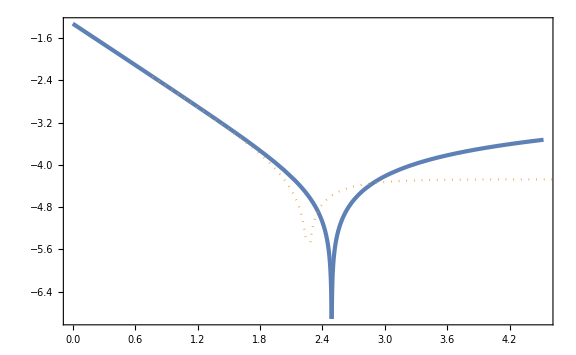

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[Abs[xsol[t]]]},{t,0,tf},PlotRange->Full],Plot[Log10[Abs[xLs+dotxLs/(3Hs)(1-Exp[-3NN])]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

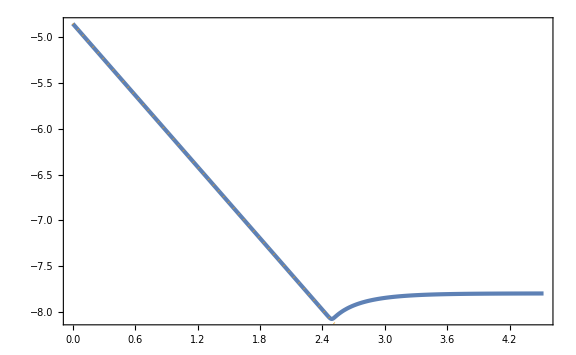

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[dotxsol[t]]},{t,0,tf},PlotRange->Full],Plot[Log10[dotxLs Exp[-3NN]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

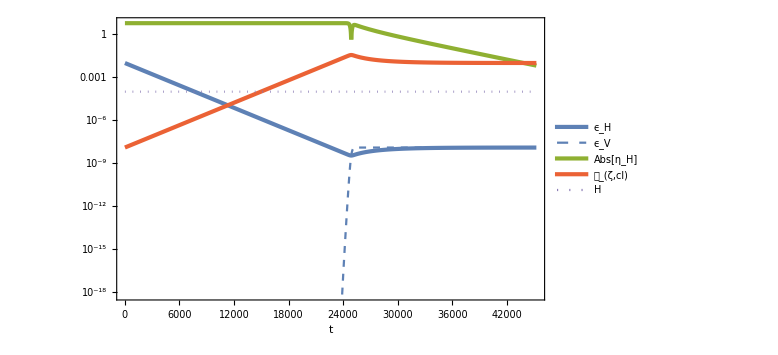

```mathematica
LogPlot[{ϵsol[t],ϵVsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hsol[t]/(2π))^2,Hsol[t]},{t,0,tf},PlotLegends->{Subscript[ϵ, H],Subscript[ϵ, V],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl],H},FrameLabel->{t,None},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},AbsoluteThickness[3],AbsoluteThickness[3],Dotted}]
```

```mathematica
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]
```

25260.0820231498318044037217849

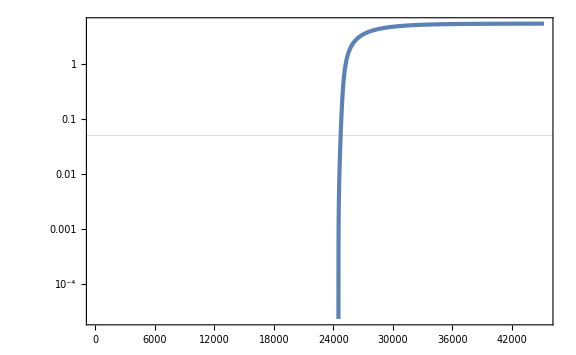

```mathematica
LogPlot[(1-dotxUSR[t]/dotxsol[t])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,0,tf},GridLines->{None,{0.05}},PlotRange->Full]
```

```mathematica
t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function (1-ⅇ^(-3 t/10000)/(50000 √2 InterpolatingFunction[{{0,45264.1389511827300420350562861}},{5,3,2,{479},{4},{1},0,0,0,Automatic,{},{},False},{{0,«49»,«429»}},{«1»},{Automatic}][t])==0.00933123191115542099952469) is less than WorkingPrecision (30.).

24748.4913022237288418280285433

```mathematica
(1-dotxUSR[t2p]/dotxsol[t2p])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params
```

0.05

```mathematica
x2p=xsol[t2p]
```

-1.1827808870656987054642963×10^-6

```mathematica
dN=Nsol[t2m]-Nsol[t2p]
```

0.0511590721181729847431768257

```mathematica
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-dNi/Hs},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p];
{dNi,dN},{logdNi,Log10[dNs]-1,Log10[dNs]+1,1/10}];//AbsoluteTiming
Clear[dNi]
```

InterpolatingFunction::dmval: Input value {47911.1640292840933952209505591} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47476.6144066751111662826672394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47476.0040528946764363138147411} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2.20475,Null}

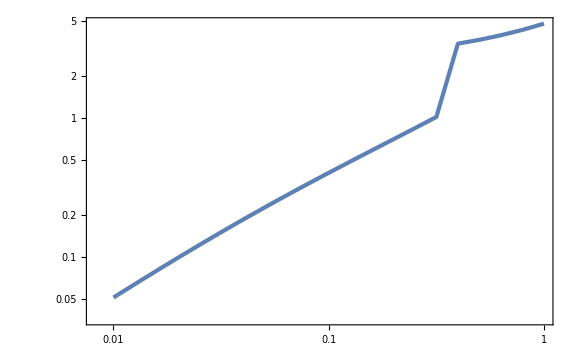

```mathematica
ListLogLogPlot[dNsList]
```

```mathematica
dNsint[dNi_]=Interpolation[dNsList][dNi];
```

```mathematica
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs},WorkingPrecision->30]
```

InterpolatingFunction::dmval: Input value {0.00752556784576483617477711592445} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.0202126048728847611599122820392

```mathematica
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]
```

0.0999999369265599351343965655

```mathematica
deltaM=√(ϵsol[t2p]/ϵVsol[t2m])
```

0.5744402841303678843211183

```mathematica
deltaeff=((dN/1.5)^3+deltaM^3)^(1/3)
```

0.574739

```mathematica
fNLM=5/2 1/(1+deltaeff)^2
```

1.00814

```mathematica
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}]
xc=xsol[tc]
```

9997.23

-0.00232008

```mathematica
Neval=Nsol[tf]-1
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]
```

3.5266913071503502871860496735

FindRoot::precw: The precision of the argument function (InterpolatingFunction[{{0,45264.1389511827300420350562861}},{5,3,1,{474},{4},0,0,0,0,Automatic,{},{},False},{{0,«49»,«424»}},{{0,0.000100166528008778128624246004569},{5.0764718919540190056223453471×10^-8,0.000100166527958097818200408657717},«48»,«424»},{Automatic}][t]==«78») is less than WorkingPrecision (30.).

0.00014028767069518981674789753912

```mathematica
tS=tc;
```

```mathematica
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];//AbsoluteTiming
```

{3.95185,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(5.4703643154683715764872924×10^-14)/x^2

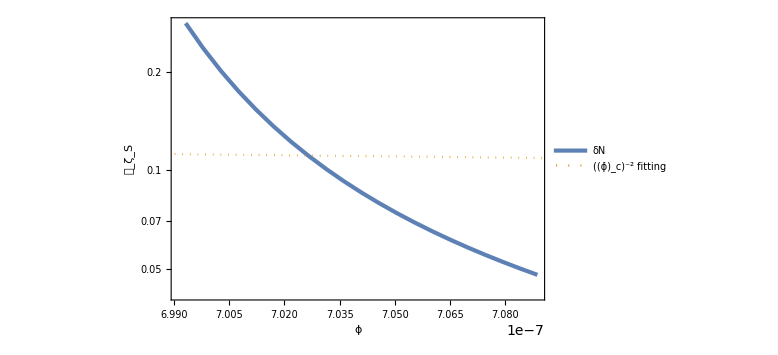

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-7,3 10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

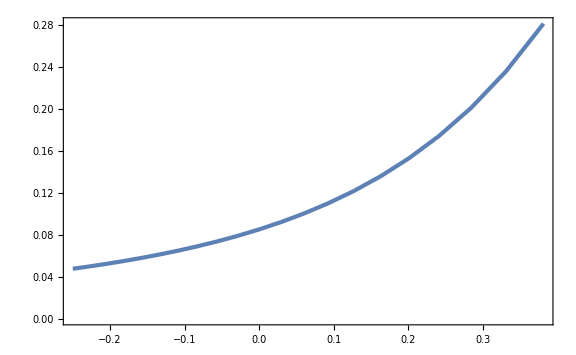

```mathematica
ListPlot[PSvszetaL]
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.085413817033409252995185683

```mathematica
fNLdN=5/12 PSvszetaLint'[0]/PS0
```

1.09818430531303856024871

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30]
dotxc=dotxsol[tc]
```

9997.23257342910069996027235966

7.040954731396723655584439×10^-7

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

113.5616333023717971805

```mathematica
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;//AbsoluteTiming
Zc
```

{0.926317,Null}

130.1764832778147923643774

```mathematica
fNLM
fNLdN
fNLS=(5power)/(4Zc)
```

1.00814

1.09818430531303856024871

1.090458415019702662615

#### dNS=0.1

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify;
dotxUSR[NN_]=dotxL Exp[-3NN];
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=1/10;
V0s=3 Hs^2;
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];
NLs=1/6 Log[ϵUSRi/ϵUSRcs];
dotxLs=dotxcs Exp[3 NLs];
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;
tf=2NLs/Hs;
```

```mathematica
fNLList=ParallelTable[
deltas=10^logdeltas;
ϵSRs=deltas^-2 ϵUSRcs;
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m-dNi/Hs},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p];
{dNi,dN},{logdNi,Log10[dNs]-1,Log10[dNs]+1,1/10}];
Clear[dNi];
dNsint[dNi_]=Interpolation[dNsList][dNi];
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs},WorkingPrecision->30]//Quiet;
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m},WorkingPrecision->30]//Quiet;
dN=Nsol[t2m]-Nsol[t2p];
deltaM=√(ϵsol[t2p]/ϵVsol[t2m]);
deltaeff=((dN/1.5)^3+deltaM^3)^(1/3);
fNLM=5/2 1/(1+deltaeff)^2;
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}];
xc=xsol[tc];
Neval=Nsol[tf]-1;
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]//Quiet;
tS=tc;
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
PS0=PSvszetaLint[0];
fNLdN=5/12 PSvszetaLint'[0]/PS0;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30];
dotxc=dotxsol[tc];
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc];
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;
fNLS=(5power)/(4Zc);
{deltaM,deltaeff,power,Zc,fNLM,fNLdN,fNLS},{logdeltas,-3,0,1/10}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {47911.1640292840933952209505591} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47476.6144066751111662826672394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47476.0040528946764363138147411} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{63.5239,Null}

```mathematica
SetDirectory["~/Documents/Univ/LOE_beyond_fNL"];
```

```mathematica
Export["fNLList_dN=0,1.dat",fNLList];
```

```mathematica
fNLMvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,1,0,0}}];
fNLdNvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,1,0}}];
fNLSvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
```

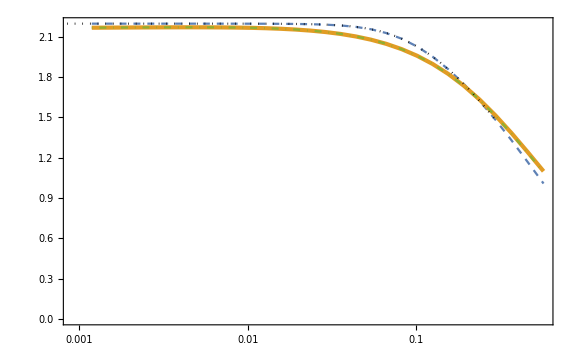

```mathematica
Show[ListLogLinearPlot[{fNLMvsdM,fNLdNvsdM,fNLSvsdM},PlotStyle->{Dashed,AbsoluteThickness[3],DotDashed}],LogLinearPlot[5/2 1/((1+((dNs/1.5)^3+dM^3)^(1/3))^2),{dM,5 10^-4,0.5},PlotStyle->{Black,Dotted}]]
```

#### dNS=0.3 practice

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
```

```mathematica
Limit[Integrate[Vp[x],x],{x->-∞}]
```

(dx V0 √ϵSR Log[2])/(√2)

```mathematica
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify
```

V0-(dx V0 √ϵSR Log[2])/(√2)-(V0 √ϵSR (x+dx Log[Cosh[x/dx]]))/(√2)

```mathematica
Limit[V[x],{x->-∞}]
```

V0

```mathematica
V'[x]-Vp[x]//Simplify
```

0

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=3/10;
```

```mathematica
deltas=10^-3;
```

```mathematica
V0s=3 Hs^2;V0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
ϵSRs=deltas^-2 ϵUSRcs;ϵSRs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[ϵUSRi/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

3.×10^-8

1.26651×10^-8

0.0126651

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNi=10^(-3/2)dNs;
dxs=dotxcs dNi/Hs;dxs//N
```

1.50988×10^-6

```mathematica
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
```

```mathematica
tf=(2NLs+20)/Hs;tf//N
```

245264.

```mathematica
x2m=2dxs;x2m//N
```

3.01975×10^-6

```mathematica
dotxUSR[t_]=dotxL Exp[-3 √(V0/3) t];
```

```mathematica
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];//AbsoluteTiming
```

$Aborted

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hsol[t] dotxsol[t])/.params;
```

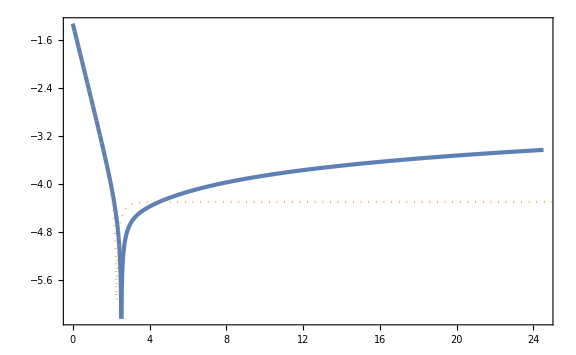

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[Abs[xsol[t]]]},{t,0,tf},PlotRange->Full],Plot[Log10[Abs[xLs-2dxs+dotxLs/(3Hs)(1-Exp[-3NN])]],{NN,0,25},PlotStyle->{Color[2],Dotted},PlotRange->Full]]
```

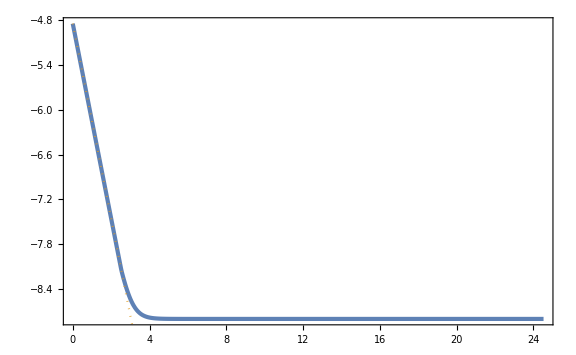

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[dotxsol[t]]},{t,0,tf},PlotRange->Full],Plot[Log10[dotxLs Exp[-3NN]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

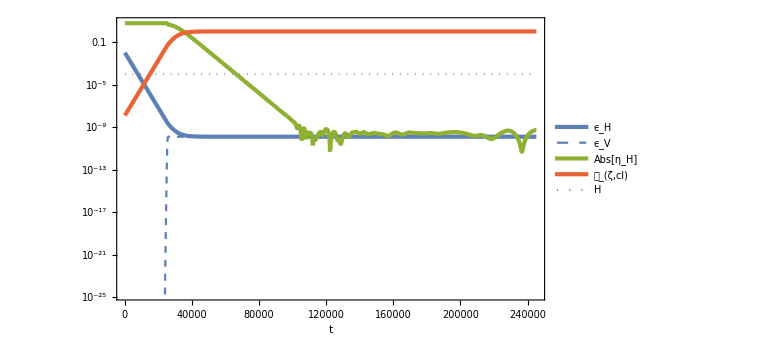

```mathematica
LogPlot[{ϵsol[t],ϵVsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hsol[t]/(2π))^2,Hsol[t]},{t,0,tf},PlotLegends->{Subscript[ϵ, H],Subscript[ϵ, V],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl],H},FrameLabel->{t,None},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},AbsoluteThickness[3],AbsoluteThickness[3],Dotted}]
```

```mathematica
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]
```

25732.1823112497244876350775548

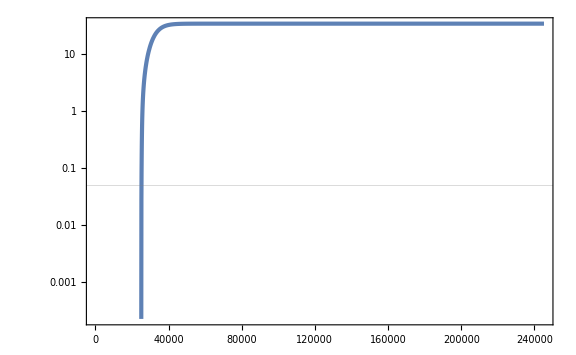

```mathematica
LogPlot[(1-dotxUSR[t]/dotxsol[t])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,0,tf},GridLines->{None,{0.05}},PlotRange->Full]
```

```mathematica
t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-Min[dNi,dNs]/Hs},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function (1-ⅇ^(-3 t/10000)/(50000 √2 InterpolatingFunction[{{0,245264.138951182730042035056286}},{5,3,2,{551},{4},{1},0,0,0,Automatic,{},{},False},{{0,«49»,«501»}},{«1»},{Automatic}][t])==0.0014654453773371896699932) is less than WorkingPrecision (30.).

25205.2056074778346609038943952

```mathematica
(1-dotxUSR[t2p]/dotxsol[t2p])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params
```

0.05

```mathematica
x2p=xsol[t2p]
```

-6.118238125326309137103444×10^-7

```mathematica
dN=Nsol[t2m]-Nsol[t2p]
```

0.0526976703974534350120786542

```mathematica
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]//Quiet;t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-Min[dNi,dNs]/Hs},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]//Quiet;
{dNi,dN},{logdNi,Log10[dNs]-3/2,Log10[dNs]+3/2,1/10}];//AbsoluteTiming
Clear[dNi]
```

{3.65287,Null}

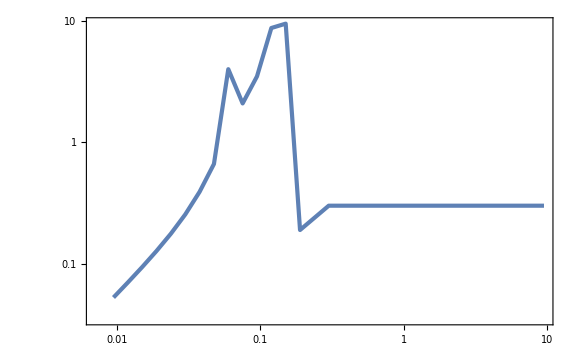

```mathematica
ListLogLogPlot[dNsList]
```

```mathematica
dNsint[dNi_]=Interpolation[dNsList,InterpolationOrder->1][dNi];
```

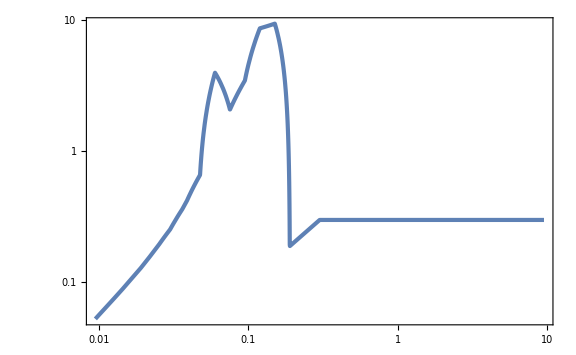

```mathematica
LogLogPlot[dNsint[dNi],{dNi,10^(-3/2)dNs,10^(3/2)dNs}]
```

```mathematica
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs/((10^2 deltas)^(1/2))},WorkingPrecision->30]
```

0.0326211709402939279468349853259

```mathematica
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-Min[dNss,dNs]/Hs},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]
```

0.294201982713918151836578201

```mathematica
deltaM=√(ϵsol[t2p]/ϵVsol[t2m])
```

3.516130067476510540042746

```mathematica
deltaeff=((dNs/1.5)^3+deltaM^3)^(1/3)
```

0.424429

```mathematica
fNLM=5/2 1/(1+deltaeff)^2
```

1.23214

```mathematica
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}]
xc=xsol[tc]
```

9997.23

-0.00233341

```mathematica
Neval=Nsol[tf]-1
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]
```

23.526688419939923326933228127

FindRoot::precw: The precision of the argument function (InterpolatingFunction[{{0,245264.138951182730042035056286}},{5,3,1,{600},{4},0,0,0,0,Automatic,{},{},False},{{0,«49»,«550»}},{{0,0.000100166528008778128624246004569},{5.41490352472577480085448168844×10^-8,0.000100166527954719129930995307329},«48»,«550»},{Automatic}][t]==«58») is less than WorkingPrecision (30.).

0.0032764751732775918433900073656

```mathematica
tS=tc;
```

```mathematica
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];//AbsoluteTiming
```

{5.32093,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(1.693230087874508248524365×10^-13)/x^2

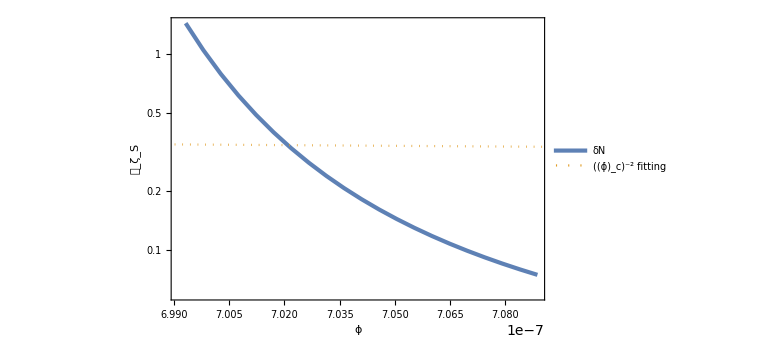

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-7,3 10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

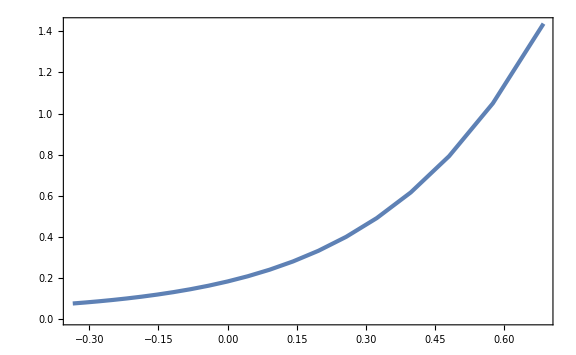

```mathematica
ListPlot[PSvszetaL]
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.1823804094227616083564123

```mathematica
fNLdN=5/12 PSvszetaLint'[0]/PS0
```

1.22679814893962189217274

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30]
dotxc=dotxsol[tc]
```

9997.23257342910332904568114825

7.0409547313975975756744118×10^-7

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

185.3576049059037115263

```mathematica
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;//AbsoluteTiming
Zc
```

{1.50512,Null}

188.64686950906837448393126

```mathematica
fNLM
fNLdN
fNLS=(5power)/(4Zc)
```

1.23214

1.22679814893962189217274

1.228204882144846923069

#### dNS=0.3

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify;
dotxUSR[NN_]=dotxL Exp[-3NN];
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=3/10;
V0s=3 Hs^2;
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];
NLs=1/6 Log[ϵUSRi/ϵUSRcs];
dotxLs=dotxcs Exp[3 NLs];
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;
tf=(2NLs+10)/Hs;
```

```mathematica
fNLList=ParallelTable[
deltas=10^logdeltas;
ϵSRs=deltas^-2 ϵUSRcs;
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]//Quiet;t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m-Min[dNi,dNs]/Hs},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]//Quiet;
{dNi,dN},{logdNi,Log10[dNs]-3/2,Log10[dNs]+3/2,1/10}];
Clear[dNi];
dNsint[dNi_]=Interpolation[dNsList,InterpolationOrder->1][dNi];
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs/((10^2 deltas)^(1/2))},WorkingPrecision->30]//Quiet;
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]//Quiet;t2p=t/.FindRoot[1-dotxUSR[Nsol[t]]/dotxsol[t]==5/100(1-dotxUSR[Nsol[t2m]]/dotxsol[t2m])/.params,{t,t2m-dNss/Hs},WorkingPrecision->30]//Quiet;
deltaM=√(ϵsol[t2p]/ϵVsol[t2m]);
deltaeff=((dNs/1.5)^3+deltaM^3)^(1/3);
fNLM=5/2 1/(1+deltaeff)^2;
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}]//Quiet;
xc=xsol[tc];
Neval=Nsol[tf]-1;
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]//Quiet;
tS=tc;
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
PS0=PSvszetaLint[0];
fNLdN=5/12 PSvszetaLint'[0]/PS0;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc];
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;
fNLS=(5power)/(4Zc);
{deltaM,deltaeff,power,Zc,fNLM,fNLdN,fNLS},{logdeltas,-3,0,1/10}];//AbsoluteTiming
```

{122.511,Null}

```mathematica
SetDirectory["~/Documents/Univ/LOE_beyond_fNL"];
```

```mathematica
Export["fNLList_dN=0,3.dat",fNLList];
```

```mathematica
fNLMvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,1,0,0}}];
fNLdNvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,1,0}}];
fNLSvsdM=fNLList.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
```

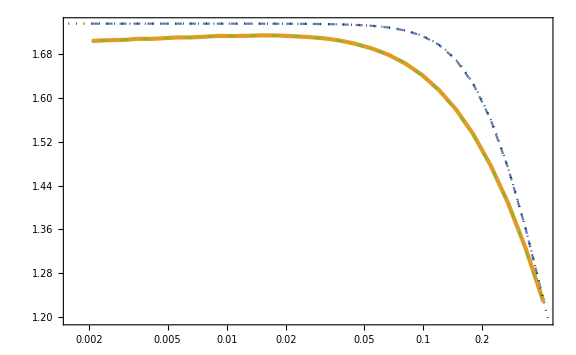

```mathematica
Show[ListLogLinearPlot[{fNLMvsdM,fNLdNvsdM,fNLSvsdM},PlotStyle->{Dashed,AbsoluteThickness[3],DotDashed},PlotRange->Full],LogLinearPlot[5/2 1/((1+((dNs/1.5)^3+dM^3)^(1/3))^2),{dM,0.001,1},PlotStyle->{Black,Dotted},PlotRange->Full]]
```

```mathematica
fNLList5em3=Import["fNLList_dN=5e-3.dat"];
```

```mathematica
fNLdNvsdM5em3=fNLList5em3.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,1,0}}];
fNLSvsdM5em3=fNLList5em3.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
```

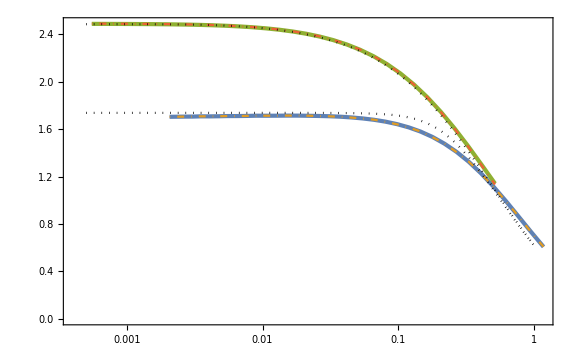

```mathematica
Show[ListLogLinearPlot[{fNLdNvsdM,fNLSvsdM,fNLdNvsdM5em3,fNLSvsdM5em3},PlotStyle->{AbsoluteThickness[3],DotDashed,AbsoluteThickness[3],DotDashed},PlotRange->Full],LogLinearPlot[{5/2 1/((1+((0.3/1.5)^3+dM^3)^(1/3))^2),5/2 1/((1+(((5 10^-3)/1.5)^3+dM^3)^(1/3))^2)},{dM,0.0005,1},PlotStyle->{{Black,Dotted}},PlotRange->Full]]
```

#### dNS=1 practice

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,V0>0,dx>0};
```

```mathematica
Vp[x_]=-(√(2ϵSR)V0)/2(1+Tanh[x/dx]);
```

```mathematica
Limit[Integrate[Vp[x],x],{x->-∞}]
```

(dx V0 √ϵSR Log[2])/(√2)

```mathematica
V[x_]=V0+Integrate[Vp[x],x]-Limit[Integrate[Vp[x],x],{x->-∞}]//Simplify
```

V0-(dx V0 √ϵSR Log[2])/(√2)-(V0 √ϵSR (x+dx Log[Cosh[x/dx]]))/(√2)

```mathematica
Limit[V[x],{x->-∞}]
```

V0

```mathematica
V'[x]-Vp[x]//Simplify
```

0

```mathematica
Hs=10^-4;
AUSRcs=10^-2;
ϵUSRi=10^-2;
dNs=1;
```

```mathematica
deltas=10^-1;
```

```mathematica
V0s=3 Hs^2;V0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
ϵSRs=deltas^-2 ϵUSRcs;ϵSRs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[ϵUSRi/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

3.×10^-8

1.26651×10^-8

1.26651×10^-6

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNi=10dNs;
dxs=dotxcs dNi/Hs;dxs//N
```

0.00159155

```mathematica
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
```

```mathematica
tf=(2NLs+30)/Hs;tf//N
```

345264.

```mathematica
x2m=2dxs;x2m//N
```

0.0031831

```mathematica
dotxUSR[t_]=dotxL Exp[-3 √(V0/3) t];
```

```mathematica
H[x_,dotx_]=√((1/2 dotx^2+V[x])/3);
```

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];//AbsoluteTiming
```

{0.155243,Null}

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hsol[t] dotxsol[t])/.params;
```

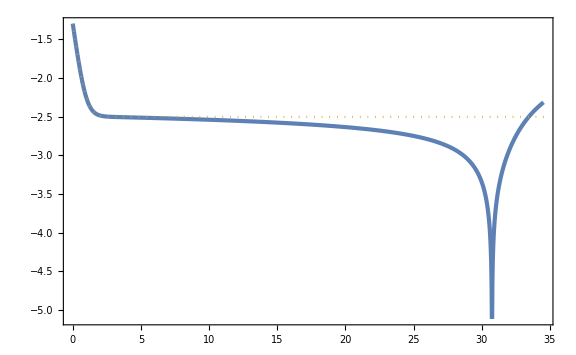

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[Abs[xsol[t]]]},{t,0,tf},PlotRange->Full],Plot[Log10[Abs[xLs-2dxs+dotxLs/(3Hs)(1-Exp[-3NN])]],{NN,0,35},PlotStyle->{Color[2],Dotted},PlotRange->Full]]
```

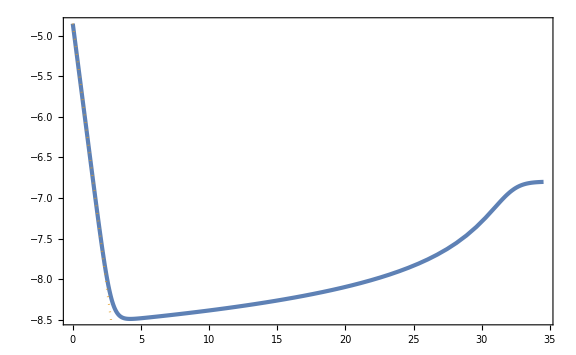

```mathematica
Show[ParametricPlot[{Nsol[t],Log10[dotxsol[t]]},{t,0,tf},PlotRange->Full],Plot[Log10[dotxLs Exp[-3NN]],{NN,0,8},PlotStyle->{Color[2],Dotted}]]
```

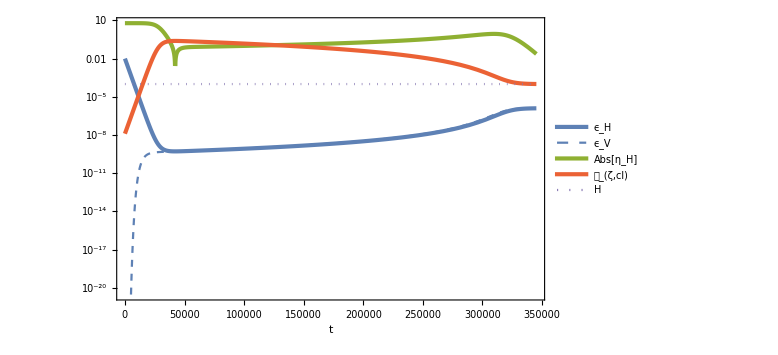

```mathematica
LogPlot[{ϵsol[t],ϵVsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hsol[t]/(2π))^2,Hsol[t]},{t,0,tf},PlotLegends->{Subscript[ϵ, H],Subscript[ϵ, V],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl],H},FrameLabel->{t,None},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},AbsoluteThickness[3],AbsoluteThickness[3],Dotted}]
```

```mathematica
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]
```

InterpolatingFunction::dmval: Input value {593962.949737661044213348556493} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {427801.350351479221327668670393} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {376836.228083435864262897536096} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

334709.283500342526013471432208

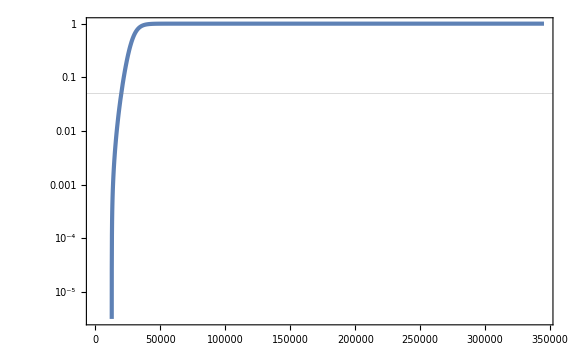

```mathematica
LogPlot[(1-dotxUSR[t]/dotxsol[t])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,0,tf},GridLines->{None,{0.05}},PlotRange->Full]
```

```mathematica
t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-dNi/(10Hs)},WorkingPrecision->30]
```

InterpolatingFunction::dmval: Input value {-2.92239355150308273412124288987×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.92239355150299967472930249227×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

324709.283500333297192144721356

```mathematica
(1-dotxUSR[t2p]/dotxsol[t2p])/(1-dotxUSR[t2m]/dotxsol[t2m])/.params
```

0.999999999999999999999999999999999999999949551415940688661252370902

```mathematica
x2p=xsol[t2p]
```

0.001737989522233799721719725176

```mathematica
dN=Nsol[t2m]-Nsol[t2p]
```

0.99999819707809920981741007

```mathematica
dNsList=Table[dNi=10^logdNi;
dxs=dotxcs dNi/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30]//Quiet;t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-dNi/(10Hs)},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]//Quiet;
{dNi,dN},{logdNi,Log10[dNs]-1,Log10[dNs]+3/2,1/10}];//AbsoluteTiming
Clear[dNi]
```

{4.22344,Null}

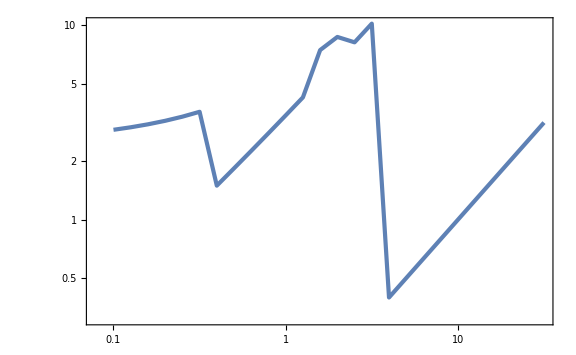

```mathematica
ListLogLogPlot[dNsList]
```

```mathematica
dNsint[dNi_]=Interpolation[dNsList,InterpolationOrder->1][dNi];
```

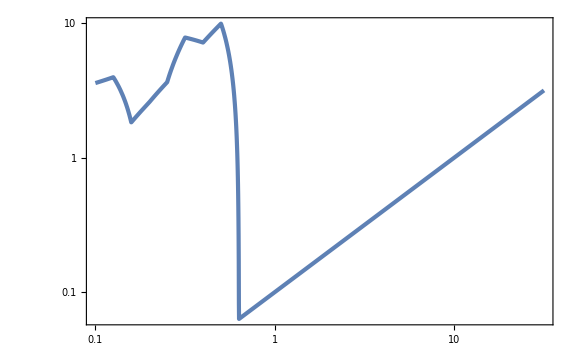

```mathematica
LogLogPlot[dNsint[dNi],{dNi,10^-1 dNs,10^(3/2)dNs}]
```

```mathematica
dNss=dNi/.FindRoot[dNsint[dNi]==dNs,{dNi,dNs},WorkingPrecision->30]
```

10.0000000591828164423250731429

```mathematica
dxs=dotxcs dNss/Hs;
params={V0->V0s,ϵSR->ϵSRs,dotxL->dotxLs,xL->xLs-2dxs,dx->dxs};
x2m=2dxs;
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=H[xsol[t],dotxsol[t]]/.params;
ϵsol[t_]=dotxsol[t]^2/(2 Hsol[t]^2);
ϵVsol[t_]=1/2(Vp[xsol[t]]/V[xsol[t]])^2/.params;
t2m=t/.FindRoot[xsol[t]==x2m,{t,NLs/Hs},WorkingPrecision->30];t2p=t/.FindRoot[1-dotxUSR[t]/dotxsol[t]==5/100(1-dotxUSR[t2m]/dotxsol[t2m])/.params,{t,t2m-dNs/(10Hs)},WorkingPrecision->30]//Quiet;dN=Nsol[t2m]-Nsol[t2p]
```

InterpolatingFunction::dmval: Input value {2.73860040654655516754312090531×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.53681865042999701980039523813×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.17143231429756943229393762007×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.099999999416817818

```mathematica
deltaM=√(ϵsol[t2p]/ϵVsol[t2m])
```

InterpolatingFunction::dmval: Input value {7.45722370211791732534615693164×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.770038940746937

```mathematica
deltaeff=((dNs/1.5)^3+deltaM^3)^(1/3)
```

0.666675

```mathematica
fNLM=5/2 1/(1+deltaeff)^2
```

0.899992

```mathematica
deltax=Hs/(2π);
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs}]
xc=xsol[tc]
```

9997.23

-0.00487233

```mathematica
Neval=Nsol[tf]-1
xeval=xsol[t/.FindRoot[Nsol[t]==Neval,{t,tf-1/Hs},WorkingPrecision->30]]
```

19.634031870752948130504424552

3.87901301139721092982810978

```mathematica
tS=tc;
```

```mathematica
dotxczetaLPS=Table[
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Nsol[t/.FindRoot[xsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-Neval;
Spsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
Smsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]-1/10 deltax,x'[tS]==dotxsol[tS],
NN'[t]==H[x[t],x'[t]],NN[tS]==Nsol[tS]}/.params,{x[t],x'[t],NN[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSpsol[t_]=x[t]/.Spsol;
NSpsol[t_]=NN[t]/.Spsol;
xSmsol[t_]=x[t]/.Smsol;
NSmsol[t_]=NN[t]/.Smsol;
ζS=5(NSmsol[t/.FindRoot[xSmsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]-NSpsol[t/.FindRoot[xSpsol[t]==xeval,{t,tf-1/Hs},WorkingPrecision->30]//Quiet]);
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];//AbsoluteTiming
```

{9.28149,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(7.02008930210220445652402×10^-17)/x^2

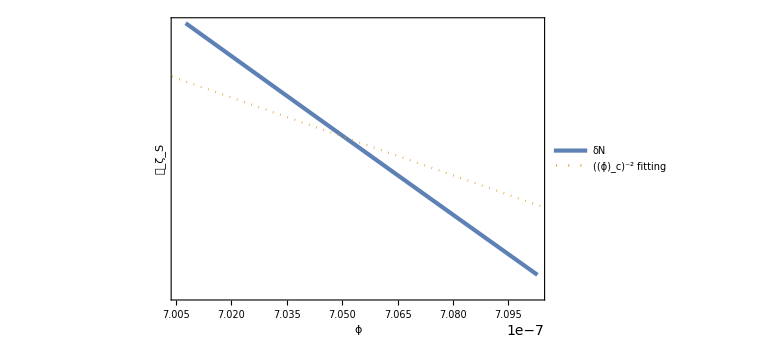

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-7,3 10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

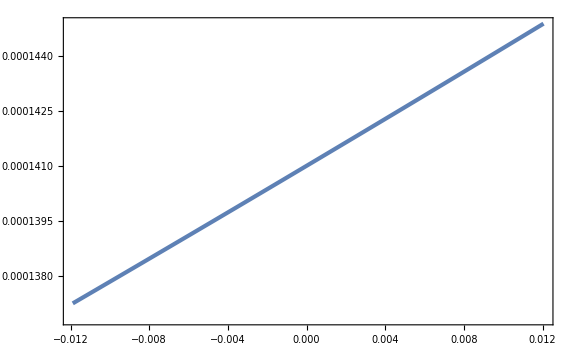

```mathematica
ListPlot[PSvszetaL]
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.000141007520646723308669737

```mathematica
fNLdN=5/12 PSvszetaLint'[0]/PS0
```

0.938477738024007846412

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]] x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL,
NN'[t]==H[x[t],x'[t]],NN[0]==0}/.params,{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Nc=1;
tc=t/.FindRoot[Nsol[t]==1,{t,1/Hs},WorkingPrecision->30]
dotxc=dotxsol[tc]
```

9997.23257855290059068290229123

7.055232902468376206186286×10^-7

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=-dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

3.99003380708163345255

```mathematica
Zc=1+3Hs dotxc^2 NIntegrate[Exp[-3(Nsol[t]-Nsol[tc])]/dotxsol[t]^2,{t,tc,tf},WorkingPrecision->30]//Quiet;//AbsoluteTiming
Zc
```

{0.06289,Null}

5.3110041995809817698600732

```mathematica
fNLM
fNLdN
fNLS=(5power)/(4Zc)
```

0.899992

0.938477738024007846412

0.939095898143996970829

#### Plot

```mathematica
SetDirectory["~/Documents/Univ/LOE_beyond_fNL"];
```

```mathematica
fNL5em3=Import["fNLList_dN=5e-3.dat"];
fNL01=Import["fNLList_dN=0,1.dat"];
fNL03=Import["fNLList_dN=0,3.dat"];
```

```mathematica
fNLSvsdM5em3=fNL5em3.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
fNLSvsdM01=fNL01.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
fNLSvsdM03=fNL03.Transpose[{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}];
```

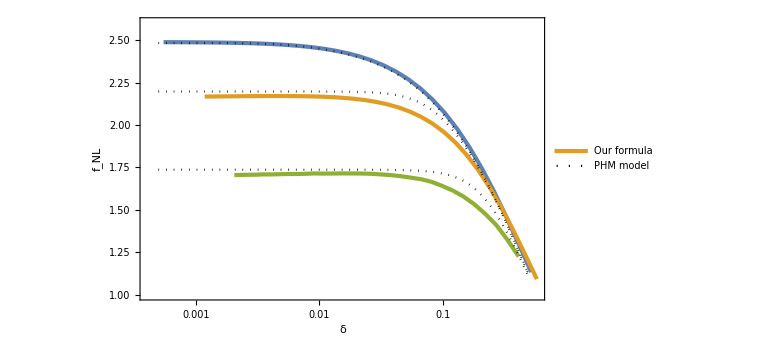

```mathematica
Show[ListLogLinearPlot[{fNLSvsdM5em3,fNLSvsdM01,fNLSvsdM03},PlotRange->{1,2.6},FrameLabel->{δ,Subscript[f, NL]},FrameTicks->{Automatic,{{{4 10^-4,"",{0.005,0}},{5 10^-4,"",{0.01,0}},{6 10^-4,"",{0.005,0}},{7 10^-4,"",{0.005,0}},{8 10^-4,"",{0.005,0}},{9 10^-4,"",{0.005,0}},{10^-3,"10^-3",{0.01,0}},{2 10^-3,"",{0.005,0}},{3 10^-3,"",{0.005,0}},{4 10^-3,"",{0.005,0}},{5 10^-3,"",{0.01,0}},{6 10^-3,"",{0.005,0}},{7 10^-3,"",{0.005,0}},{8 10^-3,"",{0.005,0}},{9 10^-3,"",{0.005,0}},{10^-2,"10^-2",{0.01,0}},{2 10^-2,"",{0.005,0}},{3 10^-2,"",{0.005,0}},{4 10^-2,"",{0.005,0}},{5 10^-2,"",{0.01,0}},{6 10^-2,"",{0.005,0}},{7 10^-2,"",{0.005,0}},{8 10^-2,"",{0.005,0}},{9 10^-2,"",{0.005,0}},{10^-1,"10^-1",{0.01,0}},{2 10^-1,"",{0.005,0}},{3 10^-1,"",{0.005,0}},{4 10^-1,"",{0.005,0}},{0.5,0.5,{0.01,0}},{0.6,"",{0.005,0}}},Automatic}},PlotLegends->Placed[LineLegend[{"","Our formula",""},LegendMarkerSize->30],{0.2,0.2}]],LogLinearPlot[{5/2 1/((1+(((5 10^-3)/1.5)^3+dM^3)^(1/3))^2),5/2 1/((1+((0.1/1.5)^3+dM^3)^(1/3))^2),5/2 1/((1+((0.3/1.5)^3+dM^3)^(1/3))^2) },{dM,5 10^-4,0.5},PlotStyle->{{Black,Dotted}},PlotLegends->Placed[LineLegend[{"PHM model"},LegendMarkerSize->30],{0.2,0.1}]]]
```

```mathematica
Solve[5/2 1/(1+dN/1.5)^2==2.1,dN]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{dN→-3.13663},{dN→0.136634}}

### Plot

```mathematica
xUSR[t_,dxL_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL+dxL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H (dxL+xL))/(3 H)

```mathematica
dotxUSR[t_,dxL_]=D[xUSR[t,dxL], t]//Simplify;
```

```mathematica
tcUSR[dxL_]=t/.Solve[xUSR[t,dxL]==xc,t][[1]]/.{C[1]->0}
```

(3 H tL+Log[dotxL/(dotxL+3 dxL H-3 H xc+3 H xL)])/(3 H)

```mathematica
xSR[t_,dxL_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-m^2(x[t]-xc)==0,x[tcUSR[dxL]]==xc,x'[tcUSR[dxL]]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->dotxUSR[tcUSR[dxL],dxL]}//Simplify
```

1/(√(9 H^2+4 m^2) (dotxL+3 H (dxL-xc+xL)))(dotxL^2 ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL)) (dotxL/(dotxL+3 H (dxL-xc+xL)))^(-(9 H+√(9 H^2+4 m^2))/(6 H))-dotxL^2 ⅇ^(-1/2 (3 H+√(9 H^2+4 m^2)) (t-tL)) (dotxL/(dotxL+3 H (dxL-xc+xL)))^(1/6 (-9+(√(9 H^2+4 m^2))/H))+√(9 H^2+4 m^2) xc (dotxL+3 H (dxL-xc+xL)))

```mathematica
dotxSR[t_,dxL_]=D[xSR[t,dxL], t]//Simplify;
```

```mathematica
params={H->1,m->0.95,xL->0,dotxL->0.1,tL->0,tc->0.5,xc->xUSR[tc,0],dxL->0.005,tcbar->tcUSR[dxL],tf->10tc};
```

```mathematica
{xUSR[tc,dxL]/.params/.params,Log10[dotxUSR[tc,dxL]]/.params/.params}
```

{0.0308957,-1.65144}

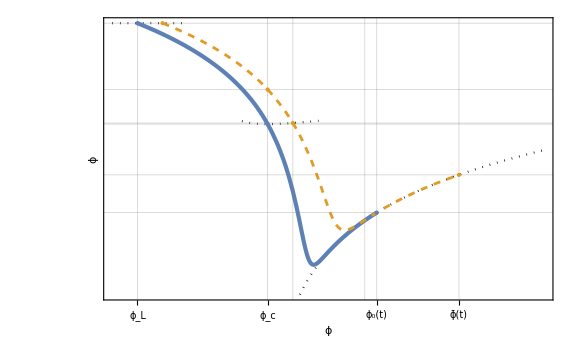

```mathematica
Show[ParametricPlot[{{xUSR[0,dxLp]/.params,Log10[dotxUSR[0,dxLp]]/.params},
{xSR[tf,dxLp]/.params/.params,Log10[dotxSR[tf,dxLp]]/.params/.params}},
{dxLp,-0.005,0.01},
PlotStyle->{{Black,Dotted}},FrameTicks->{None,{{{xL/.params,Subscript[ϕ, "L"]},{xc/.params/.params,Subscript[ϕ, "c"]},{xSR[tf,0]/.params/.params,Subscript[ϕ, 0][t]},{xSR[tf,dxL]/.params/.params/.params,OverBar[ϕ][t]}},None}}],ParametricPlot[{xSR[tc,dxLp]/.params/.params,Log10[dotxSR[tc,dxLp]]/.params/.params},
{dxLp,-0.005,0.01},
PlotStyle->{Black,Dotted}],
(*ParametricPlot[{xUSR[tc,dxLp]/.params/.params,Log10[dotxUSR[tc,dxLp]]/.params/.params},
{dxLp,-0.005,0},
PlotStyle->{Black,Dotted}],*)
ParametricPlot[{xUSR[t,0]/.params,Log10[dotxUSR[t,0]]/.params},
{t,0,tc/.params},
PlotStyle->{AbsoluteThickness[3]}],
ParametricPlot[{xSR[t,0]/.params/.params,Log10[dotxSR[t,0]]/.params/.params},
{t,tc/.params,tf/.params/.params},
PlotStyle->{AbsoluteThickness[3]}],
ParametricPlot[{xUSR[t,dxL]/.params/.params,Log10[dotxUSR[t,dxL]]/.params/.params},
{t,0,tcbar/.params/.params/.params},
PlotStyle->{Color[2],Dashed,AbsoluteThickness[2]}],
ParametricPlot[{xSR[t,dxL]/.params/.params/.params,Log10[dotxSR[t,dxL]]/.params/.params/.params},
{t,tcbar/.params/.params/.params,tf/.params/.params},
PlotStyle->{Color[2],Dashed,AbsoluteThickness[2]}],
ListPlot[{{xSR[tf,0]/.params/.params/.params,Log10[dotxSR[tf,0]]/.params/.params/.params},
{xL/.params,Log10[dotxL]/.params},
{xUSR[tc,0]/.params,Log10[dotxUSR[tc,0]]/.params}},
PlotStyle->Directive[Color[1],PointSize->Large],Joined->False],
ListPlot[{{xSR[tf,dxL]/.params/.params/.params,Log10[dotxSR[tf,dxL]]/.params/.params/.params},
{xL+dxL/.params,Log10[dotxL]/.params},
{xUSR[tcUSR[dxL],dxL]/.params/.params,Log10[dotxUSR[tcUSR[dxL],dxL]]/.params/.params},
{xSR[tc,dxL]/.params/.params,Log10[dotxSR[tc,dxL]]/.params/.params}},
PlotStyle->Directive[Color[2],PointSize->Large],
Joined->False],
PlotRange->Full,Axes->None,FrameLabel->{ϕ,OverDot[ϕ]},GridLines->{{xL/.params,xUSR[tc,0]/.params,0.95xSR[tf,0]/.params/.params/.params,xSR[tf,0]/.params/.params/.params,xSR[tf,dxL]/.params/.params/.params,xSR[tc,dxL]/.params/.params},
{Log10[dotxL]/.params,Log10[dotxSR[tf,0]]/.params/.params/.params,Log10[dotxSR[tf,dxL]]/.params/.params/.params,Log10[dotxUSR[tc,0]]/.params,Log10[dotxSR[tc,dxL]]/.params/.params,Log10[dotxUSR[tcUSR[dxL],dxL]]/.params/.params}}]
```

### linear slope uniform-dotphi

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-(√(2ϵ0))/Mpl V0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc],√(2ϵ0)->π0/(Mpl H),V0->3 Mpl^2 H^2}/.{V0->3 Mpl^2 H^2}//Simplify
```

(dotxL (-ⅇ^(3 H (-t+tL))+ⅇ^(3 H (-tc+tL)))+(-1+ⅇ^(3 H (-t+tc))) π0+3 H (xc+t π0-tc π0))/(3 H)

```mathematica
η1[t_]=xSR''[t]/(H xSR'[t])//Simplify
η2[t_]=η1'[t]/(H η1[t])//Simplify
```

(-3 dotxL ⅇ^(3 H tL)+3 ⅇ^(3 H tc) π0)/(dotxL ⅇ^(3 H tL)+(ⅇ^(3 H t)-ⅇ^(3 H tc)) π0)

-(3 ⅇ^(3 H t) π0)/(dotxL ⅇ^(3 H tL)+(ⅇ^(3 H t)-ⅇ^(3 H tc)) π0)

```mathematica
(3+η1[t]+η2[t])/η1[t]//Simplify
```

0

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 dxL H+3 H xL-π0+3 H t π0-3 H tL π0+(dotxL ⅇ^(3 H (-t+tL)) π0)/(dotxL+3 H (dxL-xc+xL))-π0 Log[dotxL/(dotxL+3 H (dxL-xc+xL))])/(3 H)

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR'[t+δ xi0]==xSR'[t]/.{dxL->δ dxL}]/.{tc->tcUSR}]
```

dotxL (ⅇ^(3 H (-t+tL)) (-1+π0/(dotxL-3 H xc+3 H xL))+ⅇ^(-3 H (t-tL+xi0 δ)) (1-π0/(dotxL+3 H (-xc+xL+dxL δ))))==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{δ,0,1}]]/.{δ->1}//Simplify
```

3 dotxL ⅇ^(3 H (-t+tL)) H ((dxL π0)/(dotxL+3 H (-xc+xL))^2+xi0 (-1+π0/(dotxL-3 H xc+3 H xL)))==0

```mathematica
xi0SR[t_]=xi0/.Simplify[Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(dxL π0)/(dotxc^2-dotxc π0)

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=Simplify[xi0/.Solve[xbarUSR'[t+xi0]==xUSR'[t],xi0][[1]]/.{C[1]->0},{H>0,t>tL}]
```

0

#### Calculate P’s correction

```mathematica
dxLUSR[t_]=xbarUSR[t+xi0USR[t]]-xUSR[t]
```

dxL

```mathematica
tcUSR
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
dxLSR[t_]=Simplify[Normal[Series[xbarSR[t+xi0SR[t]]-xSR[t]/.{dxL->ϵ dxL},{ϵ,0,1}]]/.{ϵ->1}/.{tc->tcUSR}/.{xc->xL+(dotxL-dotxc)/(3H)}/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ π0},{H>0,tc>tL}]
```

(dxL δ)/(-1+δ)

```mathematica
Simplify[Limit[(xi0SR[t]-dxLSR[t]/xSR'[t])/xi0SR[t],{t->∞},Assumptions->{H>0}]/.{dotxc->δ π0}]
```

1-δ^2

```mathematica
Zcintegrand[δ_]=Simplify[3H dotxc^2 Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ π0}//Simplify
```

(3 ⅇ^(3 H (t-tc)) H δ^2)/((-1+ⅇ^(3 H (t-tc))+δ)^2)

```mathematica
Integrate[Zcintegrand[δ],t]/.{t->tc}
```

-δ

```mathematica
Zc[δ_]=1+Limit[Integrate[Zcintegrand[δ],t],{t->∞},Assumptions->{H>0}]-Integrate[Zcintegrand[δ],t]/.{t->tc}
```

1+δ